```mathematica
pivots[A_]:=Flatten[FirstPosition[1]/@Transpose[A]]
```

```mathematica
pMatrix[n_]:=Table[
Which[i==2&&j==1||i==1&&j==2,-1/2,
i==j&&i>2,1,
True,0],{i, n},{j,n}]
```

```mathematica
gramMatrix[W_]:=Simplify[Transpose[W].pMatrix[Length[W]].W]
```

```mathematica
linearRelationsMatrix[G_]:=RowReduce[G][[1;;MatrixRank[G]]]//Transpose
```

```mathematica
linearRelations[L_]:=Select[
Table[Equal[Subscript[b, i],L[[i]].Table[Subscript[b, i],{i,pivots[L]}]],{i,Length[L]}],Not[BooleanQ[#]]&]
```

```mathematica
linearRelationsFromW=linearRelations@*linearRelationsMatrix@*gramMatrix;
```

```mathematica
inverseLinearRelations[G_]:=Table[If[i==#,1,0],{i,Length[G[[1]]]}]&/@Flatten[FirstPosition[#,1]&/@(RowReduce[G]//Select[Not[AllTrue[#,#==0&]]&])]
```

```mathematica
quadraticFormMatrix[G_,L_]:=Inverse[Table[G[[i, j]],{i,pivots[L]},{j,pivots[L]}]]
```

```mathematica
quadraticForm[Q_,L_]:=Module[{v=Table[Subscript[b, i],{i,pivots[L]}]},Simplify[v.Q.v==0]]
```

```mathematica
quadform[W_]:=Module[{G=gramMatrix[W]},Module[{L=linearRelationsMatrix[G]},quadraticForm[quadraticFormMatrix[G,L],L]]]
```

```mathematica
quadformFromG[G_]:=Module[{L=linearRelationsMatrix[G]},quadraticForm[quadraticFormMatrix[G,L],L]]
```

```mathematica
graphFromG[G_]:=PlanarGraph[AdjacencyGraph[If[#==-1,1,0]&/@#&/@G,VertexLabels->"Name"]]
```

```mathematica
nextCandidate[s_,t_,adj_]:=Block[{length,pos},length=Length[adj];
pos=Mod[Position[adj,s][[1,1]]+1,length,1];
{t,adj[[pos]]}];
```

```mathematica
FindFace[g_?PlanarGraphQ]:=Block[{emb},emb=GraphEmbedding[g,"PlanarEmbedding"];
FindFace[g,emb]];

FindFace[g_?PlanarGraphQ,emb_]:=Block[{m,orderings,pAdj,rightF,s,t,initial,face},m=AdjacencyMatrix[g];
Table[pAdj[v]=SortBy[Pick[VertexList[g],m[[v]],1],ArcTan@@(emb[[v]]-emb[[#]])&],{v,VertexList[g]}];
rightF[_]:=False;
Reap[Table[If[!rightF[e],s=e[[1]];
t=e[[2]];
initial=s;
face={s};
While[t=!=initial,rightF[UndirectedEdge[s,t]]=True;
{s,t}=nextCandidate[s,t,pAdj[t]];
face=Join[face,{s}];];
Sow[face];],{e,EdgeList[g]}]][[2,1]]]
```

```mathematica
findGenerators[faces_,vertices_,G_]:=Table[Block[{face,otherVertex,verticesOnFace,allVertices,Gp,P,Gnew,L,Q,Qform,sol1,sol2,sols,coeff,coeffTable,small,Li,P2},
face=faces[[i]];
verticesOnFace=Sort[RandomSample[face,3]];
otherVertex=RandomChoice[Select[vertices,Not[MemberQ[face,#]]&]];
allVertices=Append[verticesOnFace,otherVertex];
P=Transpose[IdentityMatrix[Length[vertices]][[#]]&/@DeleteDuplicates[Join[allVertices,vertices]]];
Gnew=Transpose[P].G.P;
L=linearRelationsMatrix[Gnew];
Gp=Table[G[[i,j]],{i,allVertices},{j,allVertices}];
Q=Inverse[Gp];
Qform=(#.Q.#&[Table[Subscript[b, j],{j,allVertices}]])==0;
sols=Expand[FullSimplify[Total[#[[1]][[2]]&/@Solve[Qform,Subscript[b, otherVertex]]]]];
coeff=Table[sols/.Table[Subscript[b, i]->If[i==curr,1,0],{i,allVertices}],{curr,allVertices}];
small=IdentityMatrix[Length[allVertices]];
small[[-1]]=Table[If[j==4,-1,If[MemberQ[verticesOnFace,allVertices[[j]]],coeff[[j]],0]],{j,Length[allVertices]}];
Li=Table[Table[If[j==k,1,0],{j,Length[vertices]}],{k,allVertices}];
P2=Table[If[j==k,1,0],{j,Length[vertices]},{k,DeleteDuplicates[Join[allVertices,vertices]]}];
P2.L.small.Li
],{i,Length[faces]}]
```

```mathematica
findGeneratorsN[faces_,vertices_,G_]:=Table[Block[{face,otherVertex,verticesOnFace,allVertices,Gp,P,Gnew,L,Q,Qform,sol1,sol2,sols,coeff,coeffTable,small,Li,P2},
face=faces[[i]];
verticesOnFace=Sort[RandomSample[face,3]];
otherVertex=RandomChoice[Select[vertices,Not[MemberQ[face,#]]&]];
allVertices=Append[verticesOnFace,otherVertex];
P=Transpose[IdentityMatrix[Length[vertices]][[#]]&/@DeleteDuplicates[Join[allVertices,vertices]]];
Gnew=Transpose[P].G.P;
L=linearRelationsMatrix[Gnew];
Gp=Table[G[[i,j]],{i,allVertices},{j,allVertices}];
Q=Inverse[Gp];
Qform=(#.Q.#&[Table[Subscript[b, j],{j,allVertices}]])==0;
sols=Expand[FullSimplify[Total[#[[1]][[2]]&/@NSolve[Qform,Subscript[b, otherVertex]]]]];
coeff=Table[sols/.Table[Subscript[b, i]->If[i==curr,1,0],{i,allVertices}],{curr,allVertices}];
small=IdentityMatrix[Length[allVertices]];
small[[-1]]=Table[If[j==4,-1,If[MemberQ[verticesOnFace,allVertices[[j]]],coeff[[j]],0]],{j,Length[allVertices]}];
Li=Table[Table[If[j==k,1,0],{j,Length[vertices]}],{k,allVertices}];
P2=Table[If[j==k,1,0],{j,Length[vertices]},{k,DeleteDuplicates[Join[allVertices,vertices]]}];
P2.L.small.Li
],{i,Length[faces]}]
```

```mathematica
findGeneratorsFromG[G_]:=findGeneratorsN[FindFace[PlanarGraph[AdjacencyGraph[If[#==-1,1,0]&/@#&/@G,VertexLabels->"Name"]]],Range[Length[G]],G]
```

```mathematica
search[generators_,current_,lastgen_,upperBound_,faces_]:=Block[{totals,invalid},
invalid[σ_,face_]:=σ==lastgen||AllTrue[Delete[σ.current,{#}&/@face],#>upperBound&];
totals[i_]:=If[invalid[generators⟦i⟧,faces⟦i⟧],0,Length[current]-Length[faces⟦i⟧]-Length[Select[Delete[current,{#}&/@faces⟦i⟧],#>upperBound&]]+search[generators,generators⟦i⟧.current,generators⟦i⟧,upperBound,faces]];
Total[totals/@Range[Length[generators]]]]
```

```mathematica
$RecursionLimit=16384
```

16384

```mathematica
fractalDimensionFromG[G_,max_,delta_,root_]:=Block[{xs,ys,data,graph,faces,sigmas,nlm,params},
xs=Range[delta,max,delta];
graph=graphFromG[G];
faces=FindFace[graph];
sigmas=findGeneratorsFromG[G];
ys=search[sigmas,root,{},#,faces]+Length[root]&/@xs;
data={xs⟦#⟧,ys⟦#⟧}&/@Range[Length[ys]];
nlm=NonlinearModelFit[data,a x^b,{a,b},x];
params=nlm["BestFitParameters"];
Print[nlm["RSquared"]];
b/.params
]
```

```mathematica
pyramidG[n_]:=Table[Which[i==0&&j==0,1,i==0||j==0,-1,True,1-(2 Sin[(Abs[i-j]π)/n]^2)/Sin[π/n]^2],{i,0,n},{j,0,n}]
```

```mathematica
pyramidG[5]//Simplify//MatrixForm
```

(1 | -1 | -1 | -1 | -1 | -1
-1 | 1 | -1 | -2-√5 | -2-√5 | -1
-1 | -1 | 1 | -1 | -2-√5 | -2-√5
-1 | -2-√5 | -1 | 1 | -1 | -2-√5
-1 | -2-√5 | -2-√5 | -1 | 1 | -1
-1 | -1 | -2-√5 | -2-√5 | -1 | 1)

```mathematica
pyramidFractalDimension[n_,max_,delta_]:=fractalDimensionFromG[N[pyramidG[n]],max,delta,N[Table[If[i==n+1,-1,(Sec[π/n]+Tan[π/n])/Tan[π/n]],{i,n+1}]]]
```

```mathematica
G={{1,-8-3 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),3 (-2-Sqrt[5]),-2-Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),-1,-1,-1,-5-2 Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5]},{-8-3 Sqrt[5],1,-5-2 Sqrt[5],-5-2 Sqrt[5],-1,-1,-5-2 Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-1,3 (-2-Sqrt[5]),3 (-2-Sqrt[5]),3 (-2-Sqrt[5]),-2-Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-2-Sqrt[5]},{-2-Sqrt[5],-5-2 Sqrt[5],1,3 (-2-Sqrt[5]),-2-Sqrt[5],3 (-2-Sqrt[5]),-1,-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-1,-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-1,-8-3 Sqrt[5]},{-2-Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),1,3 (-2-Sqrt[5]),-2-Sqrt[5],-5-2 Sqrt[5],-1,-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-1,-2-Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5],-8-3 Sqrt[5],-1},{3 (-2-Sqrt[5]),-1,-2-Sqrt[5],3 (-2-Sqrt[5]),1,-2-Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),-1,-2-Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-8-3 Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-1,-5-2 Sqrt[5]},{3 (-2-Sqrt[5]),-1,3 (-2-Sqrt[5]),-2-Sqrt[5],-2-Sqrt[5],1,-5-2 Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-5-2 Sqrt[5],-2-Sqrt[5],-1,-2-Sqrt[5],-8-3 Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-1},{-2-Sqrt[5],-5-2 Sqrt[5],-1,-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],1,-2-Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),-1,-2-Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5],-5-2 Sqrt[5],-1,-5-2 Sqrt[5],-8-3 Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5])},{-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-1,-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],1,3 (-2-Sqrt[5]),-5-2 Sqrt[5],-2-Sqrt[5],-1,3 (-2-Sqrt[5]),-5-2 Sqrt[5],-2-Sqrt[5],-1,-8-3 Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5]},{-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),-5-2 Sqrt[5],3 (-2-Sqrt[5]),1,-1,3 (-2-Sqrt[5]),-8-3 Sqrt[5],-2-Sqrt[5],-1,-2-Sqrt[5],-5-2 Sqrt[5],-1,-2-Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5]},{-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-5-2 Sqrt[5],3 (-2-Sqrt[5]),-5-2 Sqrt[5],-1,1,-8-3 Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5],-2-Sqrt[5],-1,-5-2 Sqrt[5],-2-Sqrt[5],-1,-5-2 Sqrt[5],-2-Sqrt[5]},{-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-1,-2-Sqrt[5],-1,-2-Sqrt[5],3 (-2-Sqrt[5]),-8-3 Sqrt[5],1,-1,-5-2 Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5],-5-2 Sqrt[5]},{-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-1,-2-Sqrt[5],-1,-8-3 Sqrt[5],3 (-2-Sqrt[5]),-1,1,-5-2 Sqrt[5],3 (-2-Sqrt[5]),-5-2 Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-5-2 Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5]},{3 (-2-Sqrt[5]),-1,-5-2 Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),3 (-2-Sqrt[5]),-2-Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],1,-5-2 Sqrt[5],-5-2 Sqrt[5],-8-3 Sqrt[5],-1,-1,-2-Sqrt[5],-2-Sqrt[5]},{-1,3 (-2-Sqrt[5]),-1,-5-2 Sqrt[5],-5-2 Sqrt[5],-8-3 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-1,-2-Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),-5-2 Sqrt[5],1,-2-Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5])},{-1,3 (-2-Sqrt[5]),-5-2 Sqrt[5],-1,-8-3 Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-1,3 (-2-Sqrt[5]),-5-2 Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],1,-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5]},{-1,3 (-2-Sqrt[5]),-2-Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-1,-1,-5-2 Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-8-3 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],1,3 (-2-Sqrt[5]),3 (-2-Sqrt[5]),-5-2 Sqrt[5],-5-2 Sqrt[5]},{-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-8-3 Sqrt[5],-1,-2-Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),-1,-2-Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),1,-2-Sqrt[5],-1,-5-2 Sqrt[5]},{-5-2 Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-8-3 Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-1,3 (-2-Sqrt[5]),-5-2 Sqrt[5],-1,-5-2 Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5],1,-5-2 Sqrt[5],-1},{-5-2 Sqrt[5],-2-Sqrt[5],-1,-8-3 Sqrt[5],-1,-5-2 Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-5-2 Sqrt[5],-1,-5-2 Sqrt[5],1,3 (-2-Sqrt[5])},{-5-2 Sqrt[5],-2-Sqrt[5],-8-3 Sqrt[5],-1,-5-2 Sqrt[5],-1,3 (-2-Sqrt[5]),-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-1,3 (-2-Sqrt[5]),1}}
```

{{1,-8-3 √5,-2-√5,-2-√5,3 (-2-√5),3 (-2-√5),-2-√5,-2-√5,-2-√5,-2-√5,-5-2 √5,-5-2 √5,3 (-2-√5),-1,-1,-1,-5-2 √5,-5-2 √5,-5-2 √5,-5-2 √5},{-8-3 √5,1,-5-2 √5,-5-2 √5,-1,-1,-5-2 √5,-5-2 √5,-5-2 √5,-5-2 √5,-2-√5,-2-√5,-1,3 (-2-√5),3 (-2-√5),3 (-2-√5),-2-√5,-2-√5,-2-√5,-2-√5},{-2-√5,-5-2 √5,1,3 (-2-√5),-2-√5,3 (-2-√5),-1,-5-2 √5,-2-√5,-5-2 √5,-2-√5,-5-2 √5,-5-2 √5,-1,-5-2 √5,-2-√5,-2-√5,3 (-2-√5),-1,-8-3 √5},{-2-√5,-5-2 √5,3 (-2-√5),1,3 (-2-√5),-2-√5,-5-2 √5,-1,-5-2 √5,-2-√5,-5-2 √5,-2-√5,-5-2 √5,-5-2 √5,-1,-2-√5,3 (-2-√5),-2-√5,-8-3 √5,-1},{3 (-2-√5),-1,-2-√5,3 (-2-√5),1,-2-√5,-2-√5,-5-2 √5,-5-2 √5,3 (-2-√5),-1,-2-√5,-2-√5,-5-2 √5,-8-3 √5,-5-2 √5,-2-√5,-5-2 √5,-1,-5-2 √5},{3 (-2-√5),-1,3 (-2-√5),-2-√5,-2-√5,1,-5-2 √5,-2-√5,3 (-2-√5),-5-2 √5,-2-√5,-1,-2-√5,-8-3 √5,-5-2 √5,-5-2 √5,-5-2 √5,-2-√5,-5-2 √5,-1},{-2-√5,-5-2 √5,-1,-5-2 √5,-2-√5,-5-2 √5,1,-2-√5,-5-2 √5,3 (-2-√5),-1,-2-√5,3 (-2-√5),-2-√5,-5-2 √5,-1,-5-2 √5,-8-3 √5,-2-√5,3 (-2-√5)},{-2-√5,-5-2 √5,-5-2 √5,-1,-5-2 √5,-2-√5,-2-√5,1,3 (-2-√5),-5-2 √5,-2-√5,-1,3 (-2-√5),-5-2 √5,-2-√5,-1,-8-3 √5,-5-2 √5,3 (-2-√5),-2-√5},{-2-√5,-5-2 √5,-2-√5,-5-2 √5,-5-2 √5,3 (-2-√5),-5-2 √5,3 (-2-√5),1,-1,3 (-2-√5),-8-3 √5,-2-√5,-1,-2-√5,-5-2 √5,-1,-2-√5,-2-√5,-5-2 √5},{-2-√5,-5-2 √5,-5-2 √5,-2-√5,3 (-2-√5),-5-2 √5,3 (-2-√5),-5-2 √5,-1,1,-8-3 √5,3 (-2-√5),-2-√5,-2-√5,-1,-5-2 √5,-2-√5,-1,-5-2 √5,-2-√5},{-5-2 √5,-2-√5,-2-√5,-5-2 √5,-1,-2-√5,-1,-2-√5,3 (-2-√5),-8-3 √5,1,-1,-5-2 √5,-5-2 √5,3 (-2-√5),-2-√5,-5-2 √5,3 (-2-√5),-2-√5,-5-2 √5},{-5-2 √5,-2-√5,-5-2 √5,-2-√5,-2-√5,-1,-2-√5,-1,-8-3 √5,3 (-2-√5),-1,1,-5-2 √5,3 (-2-√5),-5-2 √5,-2-√5,3 (-2-√5),-5-2 √5,-5-2 √5,-2-√5},{3 (-2-√5),-1,-5-2 √5,-5-2 √5,-2-√5,-2-√5,3 (-2-√5),3 (-2-√5),-2-√5,-2-√5,-5-2 √5,-5-2 √5,1,-5-2 √5,-5-2 √5,-8-3 √5,-1,-1,-2-√5,-2-√5},{-1,3 (-2-√5),-1,-5-2 √5,-5-2 √5,-8-3 √5,-2-√5,-5-2 √5,-1,-2-√5,-5-2 √5,3 (-2-√5),-5-2 √5,1,-2-√5,-2-√5,-2-√5,-5-2 √5,-2-√5,3 (-2-√5)},{-1,3 (-2-√5),-5-2 √5,-1,-8-3 √5,-5-2 √5,-5-2 √5,-2-√5,-2-√5,-1,3 (-2-√5),-5-2 √5,-5-2 √5,-2-√5,1,-2-√5,-5-2 √5,-2-√5,3 (-2-√5),-2-√5},{-1,3 (-2-√5),-2-√5,-2-√5,-5-2 √5,-5-2 √5,-1,-1,-5-2 √5,-5-2 √5,-2-√5,-2-√5,-8-3 √5,-2-√5,-2-√5,1,3 (-2-√5),3 (-2-√5),-5-2 √5,-5-2 √5},{-5-2 √5,-2-√5,-2-√5,3 (-2-√5),-2-√5,-5-2 √5,-5-2 √5,-8-3 √5,-1,-2-√5,-5-2 √5,3 (-2-√5),-1,-2-√5,-5-2 √5,3 (-2-√5),1,-2-√5,-1,-5-2 √5},{-5-2 √5,-2-√5,3 (-2-√5),-2-√5,-5-2 √5,-2-√5,-8-3 √5,-5-2 √5,-2-√5,-1,3 (-2-√5),-5-2 √5,-1,-5-2 √5,-2-√5,3 (-2-√5),-2-√5,1,-5-2 √5,-1},{-5-2 √5,-2-√5,-1,-8-3 √5,-1,-5-2 √5,-2-√5,3 (-2-√5),-2-√5,-5-2 √5,-2-√5,-5-2 √5,-2-√5,-2-√5,3 (-2-√5),-5-2 √5,-1,-5-2 √5,1,3 (-2-√5)},{-5-2 √5,-2-√5,-8-3 √5,-1,-5-2 √5,-1,3 (-2-√5),-2-√5,-5-2 √5,-2-√5,-5-2 √5,-2-√5,-2-√5,3 (-2-√5),-2-√5,-5-2 √5,-5-2 √5,-1,3 (-2-√5),1}}

```mathematica
(*fractalDimensionFromG[G,1000,20,{-1,2,2,4,4,7}]*)
```

```mathematica
faces-1
```

-1+faces

```mathematica
faces=FindFace[PlanarGraph[AdjacencyGraph[If[#==-1,1,0]&/@#&/@G,VertexLabels->"Name"]]]
```

{{1,14,9,10,15},{1,15,4,8,16},{1,16,7,3,14},{2,5,11,12,6},{2,6,20,18,13},{2,13,17,19,5},{3,7,11,5,19},{3,19,17,9,14},{4,15,10,18,20},{4,20,6,12,8},{7,16,8,12,11},{9,17,13,18,10}}

```mathematica
(*sigmas=findGeneratorsFromG[G]*)
```

```mathematica
(*Timing[pyramidFractalDimension[11,100000,10000]]*)
```

```mathematica
dodeca={{1,-8-3 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),3 (-2-Sqrt[5]),-2-Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),-1,-1,-1,-5-2 Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5]},{-8-3 Sqrt[5],1,-5-2 Sqrt[5],-5-2 Sqrt[5],-1,-1,-5-2 Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-1,3 (-2-Sqrt[5]),3 (-2-Sqrt[5]),3 (-2-Sqrt[5]),-2-Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-2-Sqrt[5]},{-2-Sqrt[5],-5-2 Sqrt[5],1,3 (-2-Sqrt[5]),-2-Sqrt[5],3 (-2-Sqrt[5]),-1,-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-1,-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-1,-8-3 Sqrt[5]},{-2-Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),1,3 (-2-Sqrt[5]),-2-Sqrt[5],-5-2 Sqrt[5],-1,-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-1,-2-Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5],-8-3 Sqrt[5],-1},{3 (-2-Sqrt[5]),-1,-2-Sqrt[5],3 (-2-Sqrt[5]),1,-2-Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),-1,-2-Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-8-3 Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-1,-5-2 Sqrt[5]},{3 (-2-Sqrt[5]),-1,3 (-2-Sqrt[5]),-2-Sqrt[5],-2-Sqrt[5],1,-5-2 Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-5-2 Sqrt[5],-2-Sqrt[5],-1,-2-Sqrt[5],-8-3 Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-1},{-2-Sqrt[5],-5-2 Sqrt[5],-1,-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],1,-2-Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),-1,-2-Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5],-5-2 Sqrt[5],-1,-5-2 Sqrt[5],-8-3 Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5])},{-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-1,-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],1,3 (-2-Sqrt[5]),-5-2 Sqrt[5],-2-Sqrt[5],-1,3 (-2-Sqrt[5]),-5-2 Sqrt[5],-2-Sqrt[5],-1,-8-3 Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5]},{-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),-5-2 Sqrt[5],3 (-2-Sqrt[5]),1,-1,3 (-2-Sqrt[5]),-8-3 Sqrt[5],-2-Sqrt[5],-1,-2-Sqrt[5],-5-2 Sqrt[5],-1,-2-Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5]},{-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-5-2 Sqrt[5],3 (-2-Sqrt[5]),-5-2 Sqrt[5],-1,1,-8-3 Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5],-2-Sqrt[5],-1,-5-2 Sqrt[5],-2-Sqrt[5],-1,-5-2 Sqrt[5],-2-Sqrt[5]},{-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-1,-2-Sqrt[5],-1,-2-Sqrt[5],3 (-2-Sqrt[5]),-8-3 Sqrt[5],1,-1,-5-2 Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5],-5-2 Sqrt[5]},{-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-1,-2-Sqrt[5],-1,-8-3 Sqrt[5],3 (-2-Sqrt[5]),-1,1,-5-2 Sqrt[5],3 (-2-Sqrt[5]),-5-2 Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-5-2 Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5]},{3 (-2-Sqrt[5]),-1,-5-2 Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),3 (-2-Sqrt[5]),-2-Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],1,-5-2 Sqrt[5],-5-2 Sqrt[5],-8-3 Sqrt[5],-1,-1,-2-Sqrt[5],-2-Sqrt[5]},{-1,3 (-2-Sqrt[5]),-1,-5-2 Sqrt[5],-5-2 Sqrt[5],-8-3 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-1,-2-Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),-5-2 Sqrt[5],1,-2-Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5])},{-1,3 (-2-Sqrt[5]),-5-2 Sqrt[5],-1,-8-3 Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-1,3 (-2-Sqrt[5]),-5-2 Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],1,-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5]},{-1,3 (-2-Sqrt[5]),-2-Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-1,-1,-5-2 Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-8-3 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],1,3 (-2-Sqrt[5]),3 (-2-Sqrt[5]),-5-2 Sqrt[5],-5-2 Sqrt[5]},{-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-8-3 Sqrt[5],-1,-2-Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),-1,-2-Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),1,-2-Sqrt[5],-1,-5-2 Sqrt[5]},{-5-2 Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-8-3 Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-1,3 (-2-Sqrt[5]),-5-2 Sqrt[5],-1,-5-2 Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5],1,-5-2 Sqrt[5],-1},{-5-2 Sqrt[5],-2-Sqrt[5],-1,-8-3 Sqrt[5],-1,-5-2 Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-5-2 Sqrt[5],-1,-5-2 Sqrt[5],1,3 (-2-Sqrt[5])},{-5-2 Sqrt[5],-2-Sqrt[5],-8-3 Sqrt[5],-1,-5-2 Sqrt[5],-1,3 (-2-Sqrt[5]),-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-1,3 (-2-Sqrt[5]),1}};
```

```mathematica
sigmas=findGeneratorsFromG[dodeca]
```

```mathematica
{{{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{6.854101966249684,0.,0.,0.,0.,0.,0.,0.,9.472135954999578,0.,0.,0.,0.,-3.2360679774997894,0.,0.,0.,0.,-1.6180339887498947,0.},{1.9999999999999998,0.,0.,0.,0.,0.,0.,0.,2.618033988749895,0.,0.,0.,0.,1.,0.,0.,0.,0.,-0.6180339887498948,0.},{4.618033988749894,0.,0.,0.,0.,0.,0.,0.,4.23606797749979,0.,0.,0.,0.,-3.2360679774997894,0.,0.,0.,0.,-0.6180339887498948,0.},{6.236067977499789,0.,0.,0.,0.,0.,0.,0.,8.472135954999578,0.,0.,0.,0.,-1.6180339887498947,0.,0.,0.,0.,-1.6180339887498947,0.},{7.854101966249683,0.,0.,0.,0.,0.,0.,0.,9.472135954999578,0.,0.,0.,0.,-4.236067977499789,0.,0.,0.,0.,-1.6180339887498947,0.},{4.23606797749979,0.,0.,0.,0.,0.,0.,0.,4.23606797749979,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.,0.},{5.854101966249685,0.,0.,0.,0.,0.,0.,0.,5.23606797749979,0.,0.,0.,0.,-2.618033988749895,0.,0.,0.,0.,-1.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{1.,0.,0.,0.,0.,0.,0.,0.,1.6180339887498951,0.,0.,0.,0.,-1.618033988749895,0.,0.,0.,0.,0.,0.},{6.854101966249684,0.,0.,0.,0.,0.,0.,0.,7.854101966249683,0.,0.,0.,0.,-1.6180339887498947,0.,0.,0.,0.,-1.6180339887498947,0.},{7.854101966249683,0.,0.,0.,0.,0.,0.,0.,8.472135954999578,0.,0.,0.,0.,-3.2360679774997894,0.,0.,0.,0.,-1.6180339887498947,0.},{4.23606797749979,0.,0.,0.,0.,0.,0.,0.,6.854101966249685,0.,0.,0.,0.,-2.618033988749895,0.,0.,0.,0.,-1.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.},{1.618033988749895,0.,0.,0.,0.,0.,0.,0.,1.0000000000000002,0.,0.,0.,0.,-1.618033988749895,0.,0.,0.,0.,0.,0.},{3.618033988749895,0.,0.,0.,0.,0.,0.,0.,2.6180339887498945,0.,0.,0.,0.,-0.6180339887498949,0.,0.,0.,0.,-0.6180339887498948,0.},{1.9999999999999998,0.,0.,0.,0.,0.,0.,0.,4.236067977499789,0.,0.,0.,0.,-0.6180339887498949,0.,0.,0.,0.,-0.6180339887498948,0.},{3.618033988749895,0.,0.,0.,0.,0.,0.,0.,5.236067977499789,0.,0.,0.,0.,-3.2360679774997894,0.,0.,0.,0.,-0.6180339887498948,0.},{3.23606797749979,0.,0.,0.,0.,0.,0.,0.,5.23606797749979,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.,0.},{5.854101966249685,0.,0.,0.,0.,0.,0.,0.,6.854101966249685,0.,0.,0.,0.,-4.23606797749979,0.,0.,0.,0.,-1.,0.}},{{0.,0.,0.,-1.618033988749895,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,1.618033988749895,0.,0.,0.,0.,0.},{0.,0.,0.,-10.090169943749471,0.,0.,0.,11.090169943749473,0.,0.,0.,0.,0.,-2.6180339887498945,13.090169943749476,0.,0.,0.,0.,0.},{0.,0.,0.,-9.472135954999578,0.,0.,0.,8.472135954999578,0.,0.,0.,0.,0.,-1.6180339887498947,10.090169943749475,0.,0.,0.,0.,0.},{0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,-11.708203932499366,0.,0.,0.,12.090169943749473,0.,0.,0.,0.,0.,-2.6180339887498945,13.70820393249937,0.,0.,0.,0.,0.},{0.,0.,0.,-5.236067977499789,0.,0.,0.,6.854101966249683,0.,0.,0.,0.,0.,-1.6180339887498947,7.4721359549995805,0.,0.,0.,0.,0.},{0.,0.,0.,-6.47213595499958,0.,0.,0.,6.23606797749979,0.,0.,0.,0.,0.,-1.,6.236067977499791,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,-7.854101966249683,0.,0.,0.,6.854101966249683,0.,0.,0.,0.,0.,-1.6180339887498947,10.090169943749475,0.,0.,0.,0.,0.},{0.,0.,0.,-3.8541019662496847,0.,0.,0.,3.618033988749895,0.,0.,0.,0.,0.,-1.,6.236067977499791,0.,0.,0.,0.,0.},{0.,0.,0.,-7.854101966249683,0.,0.,0.,8.472135954999578,0.,0.,0.,0.,0.,-1.6180339887498947,8.47213595499958,0.,0.,0.,0.,0.},{0.,0.,0.,-3.8541019662496847,0.,0.,0.,5.23606797749979,0.,0.,0.,0.,0.,-1.,4.618033988749896,0.,0.,0.,0.,0.},{0.,0.,0.,-10.090169943749471,0.,0.,0.,10.47213595499958,0.,0.,0.,0.,0.,-2.6180339887498945,13.70820393249937,0.,0.,0.,0.,0.},{0.,0.,0.,-6.47213595499958,0.,0.,0.,5.23606797749979,0.,0.,0.,0.,0.,-1.,7.236067977499791,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.},{0.,0.,0.,-1.618033988749895,0.,0.,0.,1.618033988749895,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.},{0.,0.,0.,-11.708203932499366,0.,0.,0.,11.090169943749473,0.,0.,0.,0.,0.,-2.6180339887498945,14.70820393249937,0.,0.,0.,0.,0.},{0.,0.,0.,-5.236067977499789,0.,0.,0.,5.854101966249683,0.,0.,0.,0.,0.,-1.6180339887498947,8.47213595499958,0.,0.,0.,0.,0.},{0.,0.,0.,-12.708203932499366,0.,0.,0.,12.090169943749473,0.,0.,0.,0.,0.,-2.6180339887498945,14.70820393249937,0.,0.,0.,0.,0.},{0.,0.,0.,-2.23606797749979,0.,0.,0.,3.618033988749895,0.,0.,0.,0.,0.,-1.,4.618033988749896,0.,0.,0.,0.,0.}},{{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-7.47213595499958,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.,10.47213595499958,0.,9.47213595499958,0.,0.,0.,0.},{-1.618033988749895,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.618033988749895,0.,1.,0.,0.,0.,0.},{-1.9999999999999996,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.6180339887498948,4.854101966249684,0.,5.236067977499789,0.,0.,0.,0.},{-6.236067977499789,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.6180339887498948,7.472135954999579,0.,6.854101966249684,0.,0.,0.,0.},{-6.47213595499958,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.,9.47213595499958,0.,9.47213595499958,0.,0.,0.,0.},{-1.618033988749895,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,1.618033988749895,0.,0.,0.,0.},{-1.8541019662496847,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.38196601125010515,3.,0.,4.23606797749979,0.,0.,0.,0.},{-1.8541019662496847,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.38196601125010515,4.618033988749895,0.,2.618033988749895,0.,0.,0.,0.},{-1.9999999999999996,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.6180339887498948,5.854101966249684,0.,4.236067977499789,0.,0.,0.,0.},{-4.47213595499958,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.38196601125010515,4.618033988749895,0.,5.23606797749979,0.,0.,0.,0.},{-4.618033988749895,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.6180339887498948,5.854101966249684,0.,6.854101966249684,0.,0.,0.,0.},{-6.47213595499958,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.,10.47213595499958,0.,8.47213595499958,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.},{-0.23606797749979025,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.38196601125010515,3.,0.,2.618033988749895,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.},{-4.618033988749895,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.6180339887498948,7.472135954999579,0.,5.236067977499789,0.,0.,0.,0.},{-4.854101966249685,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.,9.47213595499958,0.,7.854101966249685,0.,0.,0.,0.},{-4.47213595499958,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.38196601125010515,5.618033988749895,0.,4.23606797749979,0.,0.,0.,0.},{-4.854101966249685,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.,8.854101966249685,0.,8.47213595499958,0.,0.,0.,0.}},{{-1.,4.472135954999579,0.,0.,0.,0.,0.,0.,0.,0.,4.,4.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.6180339887498948,2.9999999999999996,0.,0.,0.,0.,0.,0.,0.,0.,3.854101966249684,1.2360679774997896,0.,0.,0.,0.,0.,0.,0.,0.},{-0.6180339887498948,2.9999999999999996,0.,0.,0.,0.,0.,0.,0.,0.,1.2360679774997898,3.854101966249684,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.6180339887498948,0.,0.,0.,0.,0.,0.,0.,0.,1.,-0.6180339887498948,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.6180339887498949,0.,0.,0.,0.,0.,0.,0.,0.,-0.6180339887498949,1.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.3819660112501051,1.472135954999579,0.,0.,0.,0.,0.,0.,0.,0.,2.7639320225002098,1.1458980337503153,0.,0.,0.,0.,0.,0.,0.,0.},{-0.3819660112501051,1.472135954999579,0.,0.,0.,0.,0.,0.,0.,0.,1.1458980337503153,2.7639320225002098,0.,0.,0.,0.,0.,0.,0.,0.},{-1.,5.472135954999579,0.,0.,0.,0.,0.,0.,0.,0.,4.,3.,0.,0.,0.,0.,0.,0.,0.,0.},{-1.,5.472135954999579,0.,0.,0.,0.,0.,0.,0.,0.,3.,4.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.3819660112501051,3.0901699437494736,0.,0.,0.,0.,0.,0.,0.,0.,1.1458980337503153,1.1458980337503153,0.,0.,0.,0.,0.,0.,0.,0.},{-1.,4.854101966249684,0.,0.,0.,0.,0.,0.,0.,0.,4.618033988749895,3.,0.,0.,0.,0.,0.,0.,0.,0.},{-1.,4.854101966249684,0.,0.,0.,0.,0.,0.,0.,0.,3.,4.618033988749895,0.,0.,0.,0.,0.,0.,0.,0.},{-0.6180339887498948,2.3819660112501047,0.,0.,0.,0.,0.,0.,0.,0.,2.8541019662496843,2.8541019662496843,0.,0.,0.,0.,0.,0.,0.,0.},{-0.6180339887498948,3.999999999999999,0.,0.,0.,0.,0.,0.,0.,0.,2.8541019662496843,1.2360679774997896,0.,0.,0.,0.,0.,0.,0.,0.},{-0.6180339887498948,3.999999999999999,0.,0.,0.,0.,0.,0.,0.,0.,1.2360679774997898,2.8541019662496843,0.,0.,0.,0.,0.,0.,0.,0.},{-0.3819660112501051,2.4721359549995787,0.,0.,0.,0.,0.,0.,0.,0.,2.7639320225002098,0.14589803375031551,0.,0.,0.,0.,0.,0.,0.,0.},{-0.3819660112501051,2.4721359549995787,0.,0.,0.,0.,0.,0.,0.,0.,0.14589803375031551,2.7639320225002098,0.,0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,5.236067977499789,0.,0.,0.,0.,0.,0.,5.236067977499788,0.,0.,0.,0.,2.618033988749895,-1.618033988749895,0.},{0.,0.,0.,0.,0.,0.6180339887498948,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,-0.6180339887498948,0.,0.},{0.,0.,0.,0.,0.,5.236067977499789,0.,0.,0.,0.,0.,0.,6.854101966249683,0.,0.,0.,0.,1.,-1.618033988749895,0.},{0.,0.,0.,0.,0.,2.6180339887498945,0.,0.,0.,0.,0.,0.,0.9999999999999991,0.,0.,0.,0.,1.9999999999999996,-0.6180339887498948,0.},{0.,0.,0.,0.,0.,2.6180339887498945,0.,0.,0.,0.,0.,0.,3.618033988749894,0.,0.,0.,0.,-0.6180339887498948,-0.6180339887498948,0.},{0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,5.854101966249684,0.,0.,0.,0.,0.,0.,6.236067977499788,0.,0.,0.,0.,1.,-1.618033988749895,0.},{0.,0.,0.,0.,0.,4.236067977499789,0.,0.,0.,0.,0.,0.,2.6180339887498945,0.,0.,0.,0.,1.6180339887498947,-1.,0.},{0.,0.,0.,0.,0.,2.6180339887498945,0.,0.,0.,0.,0.,0.,4.236067977499789,0.,0.,0.,0.,1.6180339887498947,-1.,0.},{0.,0.,0.,0.,0.,1.6180339887498945,0.,0.,0.,0.,0.,0.,1.9999999999999993,0.,0.,0.,0.,1.9999999999999996,-0.6180339887498948,0.},{0.,0.,0.,0.,0.,4.23606797749979,0.,0.,0.,0.,0.,0.,4.236067977499789,0.,0.,0.,0.,0.,-1.,0.},{0.,0.,0.,0.,0.,3.2360679774997894,0.,0.,0.,0.,0.,0.,1.9999999999999991,0.,0.,0.,0.,0.38196601125010515,-0.6180339887498948,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,4.854101966249684,0.,0.,0.,0.,0.,0.,6.236067977499788,0.,0.,0.,0.,2.,-1.618033988749895,0.},{0.,0.,0.,0.,0.,3.2360679774997894,0.,0.,0.,0.,0.,0.,2.6180339887498945,0.,0.,0.,0.,2.6180339887498945,-1.,0.},{0.,0.,0.,0.,0.,5.854101966249684,0.,0.,0.,0.,0.,0.,5.236067977499788,0.,0.,0.,0.,2.,-1.618033988749895,0.},{0.,0.,0.,0.,0.,1.6180339887498945,0.,0.,0.,0.,0.,0.,3.618033988749894,0.,0.,0.,0.,0.38196601125010515,-0.6180339887498948,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.},{0.,0.,0.,0.,0.,3.2360679774997894,0.,0.,0.,0.,0.,0.,5.236067977499789,0.,0.,0.,0.,0.,-1.,0.},{0.,0.,0.,0.,0.,0.6180339887498949,0.,0.,0.,0.,0.,0.,-0.6180339887498949,0.,0.,0.,0.,1.,0.,0.}},{{0.,0.,0.,0.,3.618033988749894,0.,0.,-1.,0.,0.,0.,0.,5.236067977499789,0.,0.,0.,0.,0.,3.618033988749895,0.},{0.,0.,0.,0.,0.9999999999999998,0.,0.,0.,0.,0.,0.,0.,0.6180339887498949,0.,0.,0.,0.,0.,-0.6180339887498948,0.},{0.,0.,0.,0.,1.3819660112501047,0.,0.,-0.3819660112501051,0.,0.,0.,0.,1.6180339887498942,0.,0.,0.,0.,0.,2.3819660112501047,0.},{0.,0.,0.,0.,4.618033988749894,0.,0.,-1.,0.,0.,0.,0.,5.854101966249684,0.,0.,0.,0.,0.,2.,0.},{0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,2.999999999999999,0.,0.,-0.3819660112501051,0.,0.,0.,0.,2.618033988749894,0.,0.,0.,0.,0.,-0.23606797749978958,0.},{0.,0.,0.,0.,3.236067977499789,0.,0.,-0.6180339887498948,0.,0.,0.,0.,2.618033988749894,0.,0.,0.,0.,0.,2.2360679774997894,0.},{0.,0.,0.,0.,5.236067977499789,0.,0.,-1.,0.,0.,0.,0.,5.236067977499789,0.,0.,0.,0.,0.,2.,0.},{0.,0.,0.,0.,0.38196601125010465,0.,0.,-0.3819660112501051,0.,0.,0.,0.,2.618033988749894,0.,0.,0.,0.,0.,2.3819660112501047,0.},{0.,0.,0.,0.,1.6180339887498942,0.,0.,-0.6180339887498948,0.,0.,0.,0.,4.236067977499789,0.,0.,0.,0.,0.,2.2360679774997894,0.},{0.,0.,0.,0.,2.999999999999999,0.,0.,-0.3819660112501051,0.,0.,0.,0.,1.6180339887498942,0.,0.,0.,0.,0.,0.7639320225002102,0.},{0.,0.,0.,0.,4.236067977499789,0.,0.,-0.6180339887498948,0.,0.,0.,0.,3.236067977499789,0.,0.,0.,0.,0.,0.6180339887498949,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,1.6180339887498942,0.,0.,-0.6180339887498948,0.,0.,0.,0.,3.236067977499789,0.,0.,0.,0.,0.,3.23606797749979,0.},{0.,0.,0.,0.,3.618033988749894,0.,0.,-1.,0.,0.,0.,0.,5.854101966249684,0.,0.,0.,0.,0.,3.,0.},{0.,0.,0.,0.,4.618033988749894,0.,0.,-1.,0.,0.,0.,0.,4.854101966249684,0.,0.,0.,0.,0.,3.,0.},{0.,0.,0.,0.,-0.6180339887498949,0.,0.,0.,0.,0.,0.,0.,0.6180339887498949,0.,0.,0.,0.,0.,1.,0.},{0.,0.,0.,0.,1.3819660112501047,0.,0.,-0.3819660112501051,0.,0.,0.,0.,3.236067977499789,0.,0.,0.,0.,0.,0.7639320225002102,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.},{0.,0.,0.,0.,3.236067977499789,0.,0.,-0.6180339887498948,0.,0.,0.,0.,4.236067977499789,0.,0.,0.,0.,0.,0.6180339887498949,0.}},{{-1.,0.,3.2360679774997894,0.,2.,0.,3.2360679774997894,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.6180339887498948,0.,1.3819660112501047,0.,2.8541019662496843,0.,1.3819660112501047,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-1.6180339887498947,0.,3.618033988749894,0.,4.23606797749979,0.,5.236067977499789,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-1.,0.,1.6180339887498947,0.,3.618033988749895,0.,3.2360679774997894,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-1.,0.,1.6180339887498947,0.,2.618033988749895,0.,4.23606797749979,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-1.,0.,4.236067977499789,0.,2.618033988749895,0.,1.6180339887498947,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-1.6180339887498947,0.,5.236067977499789,0.,4.23606797749979,0.,3.618033988749894,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,-0.6180339887498949,0.,0.6180339887498949,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.6180339887498948,0.,0.3819660112501049,0.,2.23606797749979,0.,2.999999999999999,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-1.,0.,3.2360679774997894,0.,3.618033988749895,0.,1.6180339887498947,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.6180339887498948,0.,2.9999999999999996,0.,1.2360679774997896,0.,1.3819660112501047,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-1.6180339887498947,0.,4.618033988749894,0.,3.8541019662496843,0.,4.618033988749894,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.6180339887498948,0.,1.3819660112501047,0.,1.2360679774997896,0.,2.999999999999999,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.6180339887498948,0.,2.9999999999999996,0.,2.23606797749979,0.,0.3819660112501049,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-1.6180339887498947,0.,4.618033988749894,0.,4.854101966249684,0.,3.618033988749894,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.9999999999999998,0.,0.6180339887498949,0.,-0.6180339887498948,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-1.6180339887498947,0.,3.618033988749894,0.,4.854101966249684,0.,4.618033988749894,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,2.618033988749895,0.,0.,0.,0.,0.,2.9999999999999996,0.,0.,0.,0.,-0.2360679774997898,0.,0.,0.,0.,0.,-0.38196601125010515},{0.,0.,6.854101966249684,0.,0.,0.,0.,0.,7.472135954999578,0.,0.,0.,0.,-6.23606797749979,0.,0.,0.,0.,0.,-0.6180339887498948},{0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,7.854101966249685,0.,0.,0.,0.,0.,9.472135954999578,0.,0.,0.,0.,-4.854101966249685,0.,0.,0.,0.,0.,-1.},{0.,0.,5.23606797749979,0.,0.,0.,0.,0.,4.618033988749895,0.,0.,0.,0.,-4.47213595499958,0.,0.,0.,0.,0.,-0.38196601125010515},{0.,0.,9.47213595499958,0.,0.,0.,0.,0.,10.472135954999578,0.,0.,0.,0.,-7.47213595499958,0.,0.,0.,0.,0.,-1.},{0.,0.,4.23606797749979,0.,0.,0.,0.,0.,2.999999999999999,0.,0.,0.,0.,-1.8541019662496847,0.,0.,0.,0.,0.,-0.38196601125010515},{0.,0.,8.47213595499958,0.,0.,0.,0.,0.,8.854101966249683,0.,0.,0.,0.,-4.854101966249685,0.,0.,0.,0.,0.,-1.},{0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,2.618033988749895,0.,0.,0.,0.,0.,4.618033988749894,0.,0.,0.,0.,-1.8541019662496847,0.,0.,0.,0.,0.,-0.38196601125010515},{0.,0.,6.854101966249684,0.,0.,0.,0.,0.,5.854101966249683,0.,0.,0.,0.,-4.618033988749894,0.,0.,0.,0.,0.,-0.6180339887498948},{0.,0.,9.47213595499958,0.,0.,0.,0.,0.,9.472135954999578,0.,0.,0.,0.,-6.47213595499958,0.,0.,0.,0.,0.,-1.},{0.,0.,4.23606797749979,0.,0.,0.,0.,0.,5.618033988749894,0.,0.,0.,0.,-4.47213595499958,0.,0.,0.,0.,0.,-0.38196601125010515},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.},{0.,0.,4.236067977499789,0.,0.,0.,0.,0.,5.854101966249683,0.,0.,0.,0.,-1.9999999999999996,0.,0.,0.,0.,0.,-0.6180339887498948},{0.,0.,5.236067977499789,0.,0.,0.,0.,0.,4.854101966249683,0.,0.,0.,0.,-1.9999999999999996,0.,0.,0.,0.,0.,-0.6180339887498948},{0.,0.,1.,0.,0.,0.,0.,0.,1.6180339887498951,0.,0.,0.,0.,-1.618033988749895,0.,0.,0.,0.,0.,0.},{0.,0.,5.236067977499789,0.,0.,0.,0.,0.,7.472135954999578,0.,0.,0.,0.,-4.618033988749894,0.,0.,0.,0.,0.,-0.6180339887498948},{0.,0.,1.618033988749895,0.,0.,0.,0.,0.,1.0000000000000002,0.,0.,0.,0.,-1.618033988749895,0.,0.,0.,0.,0.,0.},{0.,0.,8.47213595499958,0.,0.,0.,0.,0.,10.472135954999578,0.,0.,0.,0.,-6.47213595499958,0.,0.,0.,0.,0.,-1.}},{{-1.,0.,0.,3.2360679774997894,0.,0.,0.,0.,0.,4.,0.,0.,0.,0.,0.,0.,0.,-1.2360679774997896,0.,0.},{-1.6180339887498947,0.,0.,4.236067977499789,0.,0.,0.,0.,0.,3.2360679774997902,0.,0.,0.,0.,0.,0.,0.,1.618033988749895,0.,0.},{-2.6180339887498945,0.,0.,6.854101966249683,0.,0.,0.,0.,0.,7.854101966249683,0.,0.,0.,0.,0.,0.,0.,-0.6180339887498945,0.,0.},{0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-2.6180339887498945,0.,0.,6.854101966249683,0.,0.,0.,0.,0.,6.236067977499788,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.},{-1.,0.,0.,3.2360679774997894,0.,0.,0.,0.,0.,1.3819660112501055,0.,0.,0.,0.,0.,0.,0.,1.3819660112501049,0.,0.},{-2.6180339887498945,0.,0.,7.472135954999578,0.,0.,0.,0.,0.,7.23606797749979,0.,0.,0.,0.,0.,0.,0.,-0.6180339887498945,0.,0.},{-1.,0.,0.,3.8541019662496843,0.,0.,0.,0.,0.,2.381966011250105,0.,0.,0.,0.,0.,0.,0.,-0.23606797749978958,0.,0.},{-1.,0.,0.,2.2360679774997894,0.,0.,0.,0.,0.,4.,0.,0.,0.,0.,0.,0.,0.,-0.23606797749978958,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-2.6180339887498945,0.,0.,7.472135954999578,0.,0.,0.,0.,0.,6.236067977499788,0.,0.,0.,0.,0.,0.,0.,0.38196601125010554,0.,0.},{-1.6180339887498947,0.,0.,5.236067977499789,0.,0.,0.,0.,0.,3.2360679774997902,0.,0.,0.,0.,0.,0.,0.,0.6180339887498949,0.,0.},{-1.,0.,0.,2.2360679774997894,0.,0.,0.,0.,0.,2.381966011250105,0.,0.,0.,0.,0.,0.,0.,1.3819660112501049,0.,0.},{-1.6180339887498947,0.,0.,4.236067977499789,0.,0.,0.,0.,0.,5.854101966249684,0.,0.,0.,0.,0.,0.,0.,-0.9999999999999996,0.,0.},{0.,0.,0.,0.6180339887498948,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,-0.6180339887498948,0.,0.},{-1.6180339887498947,0.,0.,5.236067977499789,0.,0.,0.,0.,0.,4.854101966249684,0.,0.,0.,0.,0.,0.,0.,-0.9999999999999996,0.,0.},{-1.6180339887498947,0.,0.,3.618033988749895,0.,0.,0.,0.,0.,4.854101966249685,0.,0.,0.,0.,0.,0.,0.,0.6180339887498949,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.},{-2.6180339887498945,0.,0.,6.472135954999578,0.,0.,0.,0.,0.,7.23606797749979,0.,0.,0.,0.,0.,0.,0.,0.38196601125010554,0.,0.},{0.,0.,0.,0.6180339887498949,0.,0.,0.,0.,0.,-0.6180339887498949,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.}},{{0.,0.,0.,4.854101966249685,0.,1.9999999999999998,0.,2.23606797749979,0.,0.,0.,0.,0.,0.,-1.618033988749895,0.,0.,0.,0.,0.},{0.,0.,0.,2.381966011250105,0.,2.8541019662496847,0.,0.7639320225002103,0.,0.,0.,0.,0.,0.,-1.,0.,0.,0.,0.,0.},{0.,0.,0.,6.236067977499788,0.,4.236067977499789,0.,3.618033988749894,0.,0.,0.,0.,0.,0.,-2.6180339887498945,0.,0.,0.,0.,0.},{0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,3.2360679774997902,0.,3.6180339887498945,0.,2.23606797749979,0.,0.,0.,0.,0.,0.,-1.618033988749895,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,3.2360679774997902,0.,2.6180339887498945,0.,3.23606797749979,0.,0.,0.,0.,0.,0.,-1.618033988749895,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,7.854101966249683,0.,4.236067977499789,0.,1.9999999999999998,0.,0.,0.,0.,0.,0.,-2.6180339887498945,0.,0.,0.,0.,0.},{0.,0.,0.,5.854101966249685,0.,2.6180339887498945,0.,0.618033988749895,0.,0.,0.,0.,0.,0.,-1.618033988749895,0.,0.,0.,0.,0.},{0.,0.,0.,1.3819660112501055,0.,2.23606797749979,0.,2.381966011250105,0.,0.,0.,0.,0.,0.,-1.,0.,0.,0.,0.,0.},{0.,0.,0.,-0.6180339887498949,0.,0.6180339887498949,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,4.854101966249685,0.,3.6180339887498945,0.,0.618033988749895,0.,0.,0.,0.,0.,0.,-1.618033988749895,0.,0.,0.,0.,0.},{0.,0.,0.,7.236067977499788,0.,3.854101966249684,0.,2.9999999999999996,0.,0.,0.,0.,0.,0.,-2.6180339887498945,0.,0.,0.,0.,0.},{0.,0.,0.,4.,0.,1.2360679774997896,0.,0.7639320225002103,0.,0.,0.,0.,0.,0.,-1.,0.,0.,0.,0.,0.},{0.,0.,0.,2.381966011250105,0.,1.2360679774997896,0.,2.381966011250105,0.,0.,0.,0.,0.,0.,-1.,0.,0.,0.,0.,0.},{0.,0.,0.,7.236067977499788,0.,4.854101966249684,0.,1.9999999999999998,0.,0.,0.,0.,0.,0.,-2.6180339887498945,0.,0.,0.,0.,0.},{0.,0.,0.,4.,0.,2.23606797749979,0.,-0.2360679774997897,0.,0.,0.,0.,0.,0.,-1.,0.,0.,0.,0.,0.},{0.,0.,0.,6.236067977499788,0.,4.854101966249684,0.,2.9999999999999996,0.,0.,0.,0.,0.,0.,-2.6180339887498945,0.,0.,0.,0.,0.},{0.,0.,0.,0.9999999999999998,0.,0.6180339887498949,0.,-0.6180339887498948,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,-1.,0.,2.3819660112501047,2.2360679774997894,0.,0.,1.3819660112501055,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,-1.618033988749895,0.,0.6180339887498949,2.6180339887498945,0.,0.,5.854101966249685,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,-1.,0.,2.3819660112501047,1.2360679774997896,0.,0.,2.381966011250105,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,-1.,0.,0.7639320225002103,2.854101966249684,0.,0.,2.381966011250105,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,-1.,0.,0.7639320225002103,1.2360679774997896,0.,0.,4.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,-1.,0.,-0.2360679774997897,2.23606797749979,0.,0.,4.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,-2.618033988749895,0.,3.618033988749895,4.236067977499789,0.,0.,6.23606797749979,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,-2.618033988749895,0.,3.,4.854101966249684,0.,0.,6.23606797749979,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,-0.6180339887498948,0.6180339887498948,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,-2.618033988749895,0.,2.,4.236067977499789,0.,0.,7.854101966249685,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,-1.618033988749895,0.,3.23606797749979,2.6180339887498945,0.,0.,3.23606797749979,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,-1.618033988749895,0.,2.23606797749979,3.6180339887498945,0.,0.,3.23606797749979,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.9999999999999998,0.6180339887498948,0.,0.,-0.6180339887498948,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,-2.618033988749895,0.,3.,3.8541019662496843,0.,0.,7.23606797749979,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,-2.618033988749895,0.,2.,4.854101966249684,0.,0.,7.23606797749979,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,-1.618033988749895,0.,2.23606797749979,1.9999999999999998,0.,0.,4.854101966249685,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,-1.618033988749895,0.,0.6180339887498949,3.6180339887498945,0.,0.,4.854101966249685,0.,0.,0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,-1.,0.,0.,0.,0.,0.,0.,0.,-4.23606797749979,0.,0.,0.,6.854101966249685,5.854101966249685,0.,0.},{0.,0.,0.,0.,-0.6180339887498948,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,2.6180339887498945,2.,0.,0.},{0.,0.,0.,0.,-1.,0.,0.,0.,0.,0.,0.,0.,-2.618033988749895,0.,0.,0.,6.854101966249685,4.23606797749979,0.,0.},{0.,0.,0.,0.,-1.,0.,0.,0.,0.,0.,0.,0.,-2.618033988749895,0.,0.,0.,5.23606797749979,5.854101966249685,0.,0.},{0.,0.,0.,0.,-1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,5.23606797749979,3.2360679774997902,0.,0.},{0.,0.,0.,0.,-1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,4.23606797749979,4.23606797749979,0.,0.},{0.,0.,0.,0.,-1.6180339887498947,0.,0.,0.,0.,0.,0.,0.,-3.23606797749979,0.,0.,0.,9.472135954999578,6.854101966249685,0.,0.},{0.,0.,0.,0.,-1.6180339887498947,0.,0.,0.,0.,0.,0.,0.,-3.23606797749979,0.,0.,0.,8.472135954999578,7.854101966249685,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.618033988749895,0.,0.,0.,1.618033988749895,1.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.618033988749895,0.,0.,0.,1.,1.618033988749895,0.,0.},{0.,0.,0.,0.,-1.6180339887498947,0.,0.,0.,0.,0.,0.,0.,-1.618033988749895,0.,0.,0.,8.472135954999578,6.23606797749979,0.,0.},{0.,0.,0.,0.,-1.6180339887498947,0.,0.,0.,0.,0.,0.,0.,-1.618033988749895,0.,0.,0.,7.854101966249683,6.854101966249685,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,-0.6180339887498948,0.,0.,0.,0.,0.,0.,0.,-3.23606797749979,0.,0.,0.,5.236067977499789,3.618033988749895,0.,0.},{0.,0.,0.,0.,-0.6180339887498948,0.,0.,0.,0.,0.,0.,0.,-3.23606797749979,0.,0.,0.,4.23606797749979,4.618033988749895,0.,0.},{0.,0.,0.,0.,-1.6180339887498947,0.,0.,0.,0.,0.,0.,0.,-4.236067977499789,0.,0.,0.,9.472135954999578,7.854101966249685,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.},{0.,0.,0.,0.,-0.6180339887498948,0.,0.,0.,0.,0.,0.,0.,-0.6180339887498949,0.,0.,0.,4.23606797749979,2.,0.,0.},{0.,0.,0.,0.,-0.6180339887498948,0.,0.,0.,0.,0.,0.,0.,-0.6180339887498949,0.,0.,0.,2.6180339887498945,3.618033988749895,0.,0.}}}//RootApproximant
```

{{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/2 (7+3 √5),0,0,0,0,0,0,0,5+2 √5,0,0,0,0,-1-√5,0,0,0,0,1/2 (-1-√5),0},{2,0,0,0,0,0,0,0,1/2 (3+√5),0,0,0,0,1,0,0,0,0,1/2 (1-√5),0},{1/2 (7+√5),0,0,0,0,0,0,0,2+√5,0,0,0,0,-1-√5,0,0,0,0,1/2 (1-√5),0},{4+√5,0,0,0,0,0,0,0,4+2 √5,0,0,0,0,1/2 (-1-√5),0,0,0,0,1/2 (-1-√5),0},{1/2 (9+3 √5),0,0,0,0,0,0,0,5+2 √5,0,0,0,0,-2-√5,0,0,0,0,1/2 (-1-√5),0},{2+√5,0,0,0,0,0,0,0,2+√5,0,0,0,0,0,0,0,0,0,-1,0},{1/2 (5+3 √5),0,0,0,0,0,0,0,3+√5,0,0,0,0,1/2 (-3-√5),0,0,0,0,-1,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,1/2 (1+√5),0,0,0,0,1/2 (-1-√5),0,0,0,0,0,0},{1/2 (7+3 √5),0,0,0,0,0,0,0,1/2 (9+3 √5),0,0,0,0,1/2 (-1-√5),0,0,0,0,1/2 (-1-√5),0},{1/2 (9+3 √5),0,0,0,0,0,0,0,4+2 √5,0,0,0,0,-1-√5,0,0,0,0,1/2 (-1-√5),0},{2+√5,0,0,0,0,0,0,0,1/2 (7+3 √5),0,0,0,0,1/2 (-3-√5),0,0,0,0,-1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{1/2 (1+√5),0,0,0,0,0,0,0,1,0,0,0,0,1/2 (-1-√5),0,0,0,0,0,0},{1/2 (5+√5),0,0,0,0,0,0,0,1/2 (3+√5),0,0,0,0,1/2 (1-√5),0,0,0,0,1/2 (1-√5),0},{2,0,0,0,0,0,0,0,2+√5,0,0,0,0,1/2 (1-√5),0,0,0,0,1/2 (1-√5),0},{1/2 (5+√5),0,0,0,0,0,0,0,3+√5,0,0,0,0,-1-√5,0,0,0,0,1/2 (1-√5),0},{1+√5,0,0,0,0,0,0,0,3+√5,0,0,0,0,0,0,0,0,0,-1,0},{1/2 (5+3 √5),0,0,0,0,0,0,0,1/2 (7+3 √5),0,0,0,0,-2-√5,0,0,0,0,-1,0}},{{0,0,0,1/2 (-1-√5),0,0,0,1,0,0,0,0,0,0,1/2 (1+√5),0,0,0,0,0},{0,0,0,1/2 (-9-5 √5),0,0,0,1/2 (11+5 √5),0,0,0,0,0,1/2 (-3-√5),1/2 (15+5 √5),0,0,0,0,0},{0,0,0,-5-2 √5,0,0,0,4+2 √5,0,0,0,0,0,1/2 (-1-√5),1/2 (9+5 √5),0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-5-3 √5,0,0,0,1/2 (13+5 √5),0,0,0,0,0,1/2 (-3-√5),7+3 √5,0,0,0,0,0},{0,0,0,-3-√5,0,0,0,1/2 (7+3 √5),0,0,0,0,0,1/2 (-1-√5),3+2 √5,0,0,0,0,0},{0,0,0,-2-2 √5,0,0,0,4+√5,0,0,0,0,0,-1,4+√5,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1/2 (-9-3 √5),0,0,0,1/2 (7+3 √5),0,0,0,0,0,1/2 (-1-√5),1/2 (9+5 √5),0,0,0,0,0},{0,0,0,1/2 (-1-3 √5),0,0,0,1/2 (5+√5),0,0,0,0,0,-1,4+√5,0,0,0,0,0},{0,0,0,1/2 (-9-3 √5),0,0,0,4+2 √5,0,0,0,0,0,1/2 (-1-√5),4+2 √5,0,0,0,0,0},{0,0,0,1/2 (-1-3 √5),0,0,0,3+√5,0,0,0,0,0,-1,1/2 (7+√5),0,0,0,0,0},{0,0,0,1/2 (-9-5 √5),0,0,0,6+2 √5,0,0,0,0,0,1/2 (-3-√5),7+3 √5,0,0,0,0,0},{0,0,0,-2-2 √5,0,0,0,3+√5,0,0,0,0,0,-1,5+√5,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,1/2 (-1-√5),0,0,0,1/2 (1+√5),0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,-5-3 √5,0,0,0,1/2 (11+5 √5),0,0,0,0,0,1/2 (-3-√5),8+3 √5,0,0,0,0,0},{0,0,0,-3-√5,0,0,0,1/2 (5+3 √5),0,0,0,0,0,1/2 (-1-√5),4+2 √5,0,0,0,0,0},{0,0,0,-6-3 √5,0,0,0,1/2 (13+5 √5),0,0,0,0,0,1/2 (-3-√5),8+3 √5,0,0,0,0,0},{0,0,0,-√5,0,0,0,1/2 (5+√5),0,0,0,0,0,-1,1/2 (7+√5),0,0,0,0,0}},{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-3-2 √5,0,0,0,0,0,0,0,0,0,0,0,-1,6+2 √5,0,5+2 √5,0,0,0,0},{1/2 (-1-√5),0,0,0,0,0,0,0,0,0,0,0,0,1/2 (1+√5),0,1,0,0,0,0},{-2,0,0,0,0,0,0,0,0,0,0,0,1/2 (1-√5),1/2 (3+3 √5),0,3+√5,0,0,0,0},{-4-√5,0,0,0,0,0,0,0,0,0,0,0,1/2 (1-√5),3+2 √5,0,1/2 (7+3 √5),0,0,0,0},{-2-2 √5,0,0,0,0,0,0,0,0,0,0,0,-1,5+2 √5,0,5+2 √5,0,0,0,0},{1/2 (-1-√5),0,0,0,0,0,0,0,0,0,0,0,0,1,0,1/2 (1+√5),0,0,0,0},{1/2 (3-3 √5),0,0,0,0,0,0,0,0,0,0,0,1/2 (-3+√5),3,0,2+√5,0,0,0,0},{1/2 (3-3 √5),0,0,0,0,0,0,0,0,0,0,0,1/2 (-3+√5),1/2 (7+√5),0,1/2 (3+√5),0,0,0,0},{-2,0,0,0,0,0,0,0,0,0,0,0,1/2 (1-√5),1/2 (5+3 √5),0,2+√5,0,0,0,0},{-2 √5,0,0,0,0,0,0,0,0,0,0,0,1/2 (-3+√5),1/2 (7+√5),0,3+√5,0,0,0,0},{1/2 (-7-√5),0,0,0,0,0,0,0,0,0,0,0,1/2 (1-√5),1/2 (5+3 √5),0,1/2 (7+3 √5),0,0,0,0},{-2-2 √5,0,0,0,0,0,0,0,0,0,0,0,-1,6+2 √5,0,4+2 √5,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{2-√5,0,0,0,0,0,0,0,0,0,0,0,1/2 (-3+√5),3,0,1/2 (3+√5),0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{1/2 (-7-√5),0,0,0,0,0,0,0,0,0,0,0,1/2 (1-√5),3+2 √5,0,3+√5,0,0,0,0},{1/2 (-3-3 √5),0,0,0,0,0,0,0,0,0,0,0,-1,5+2 √5,0,1/2 (9+3 √5),0,0,0,0},{-2 √5,0,0,0,0,0,0,0,0,0,0,0,1/2 (-3+√5),1/2 (9+√5),0,2+√5,0,0,0,0},{1/2 (-3-3 √5),0,0,0,0,0,0,0,0,0,0,0,-1,1/2 (11+3 √5),0,4+2 √5,0,0,0,0}},{{-1,2 √5,0,0,0,0,0,0,0,0,4,4,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/2 (1-√5),3,0,0,0,0,0,0,0,0,1/2 (1+3 √5),-1+√5,0,0,0,0,0,0,0,0},{1/2 (1-√5),3,0,0,0,0,0,0,0,0,-1+√5,1/2 (1+3 √5),0,0,0,0,0,0,0,0},{0,1/2 (-1+√5),0,0,0,0,0,0,0,0,1,1/2 (1-√5),0,0,0,0,0,0,0,0},{0,1/2 (-1+√5),0,0,0,0,0,0,0,0,1/2 (1-√5),1,0,0,0,0,0,0,0,0},{1/2 (-3+√5),-3+2 √5,0,0,0,0,0,0,0,0,5-√5,1/2 (9-3 √5),0,0,0,0,0,0,0,0},{1/2 (-3+√5),-3+2 √5,0,0,0,0,0,0,0,0,1/2 (9-3 √5),5-√5,0,0,0,0,0,0,0,0},{-1,1+2 √5,0,0,0,0,0,0,0,0,4,3,0,0,0,0,0,0,0,0},{-1,1+2 √5,0,0,0,0,0,0,0,0,3,4,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{1/2 (-3+√5),1/2 (-5+5 √5),0,0,0,0,0,0,0,0,1/2 (9-3 √5),1/2 (9-3 √5),0,0,0,0,0,0,0,0},{-1,1/2 (3+3 √5),0,0,0,0,0,0,0,0,1/2 (7+√5),3,0,0,0,0,0,0,0,0},{-1,1/2 (3+3 √5),0,0,0,0,0,0,0,0,3,1/2 (7+√5),0,0,0,0,0,0,0,0},{1/2 (1-√5),1/2 (7-√5),0,0,0,0,0,0,0,0,1/2 (-1+3 √5),1/2 (-1+3 √5),0,0,0,0,0,0,0,0},{1/2 (1-√5),4,0,0,0,0,0,0,0,0,1/2 (-1+3 √5),-1+√5,0,0,0,0,0,0,0,0},{1/2 (1-√5),4,0,0,0,0,0,0,0,0,-1+√5,1/2 (-1+3 √5),0,0,0,0,0,0,0,0},{1/2 (-3+√5),-2+2 √5,0,0,0,0,0,0,0,0,5-√5,1/2 (7-3 √5),0,0,0,0,0,0,0,0},{1/2 (-3+√5),-2+2 √5,0,0,0,0,0,0,0,0,1/2 (7-3 √5),5-√5,0,0,0,0,0,0,0,0}},{{0,0,0,0,0,3+√5,0,0,0,0,0,0,3+√5,0,0,0,0,1/2 (3+√5),1/2 (-1-√5),0},{0,0,0,0,0,1/2 (-1+√5),0,0,0,0,0,0,1,0,0,0,0,1/2 (1-√5),0,0},{0,0,0,0,0,3+√5,0,0,0,0,0,0,1/2 (7+3 √5),0,0,0,0,1,1/2 (-1-√5),0},{0,0,0,0,0,1/2 (3+√5),0,0,0,0,0,0,1,0,0,0,0,2,1/2 (1-√5),0},{0,0,0,0,0,1/2 (3+√5),0,0,0,0,0,0,1/2 (5+√5),0,0,0,0,1/2 (1-√5),1/2 (1-√5),0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1/2 (5+3 √5),0,0,0,0,0,0,4+√5,0,0,0,0,1,1/2 (-1-√5),0},{0,0,0,0,0,2+√5,0,0,0,0,0,0,1/2 (3+√5),0,0,0,0,1/2 (1+√5),-1,0},{0,0,0,0,0,1/2 (3+√5),0,0,0,0,0,0,2+√5,0,0,0,0,1/2 (1+√5),-1,0},{0,0,0,0,0,1/2 (1+√5),0,0,0,0,0,0,2,0,0,0,0,2,1/2 (1-√5),0},{0,0,0,0,0,2+√5,0,0,0,0,0,0,2+√5,0,0,0,0,0,-1,0},{0,0,0,0,0,1+√5,0,0,0,0,0,0,2,0,0,0,0,1/2 (3-√5),1/2 (1-√5),0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,1/2 (3+3 √5),0,0,0,0,0,0,4+√5,0,0,0,0,2,1/2 (-1-√5),0},{0,0,0,0,0,1+√5,0,0,0,0,0,0,1/2 (3+√5),0,0,0,0,1/2 (3+√5),-1,0},{0,0,0,0,0,1/2 (5+3 √5),0,0,0,0,0,0,3+√5,0,0,0,0,2,1/2 (-1-√5),0},{0,0,0,0,0,1/2 (1+√5),0,0,0,0,0,0,1/2 (5+√5),0,0,0,0,1/2 (3-√5),1/2 (1-√5),0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,1+√5,0,0,0,0,0,0,3+√5,0,0,0,0,0,-1,0},{0,0,0,0,0,1/2 (-1+√5),0,0,0,0,0,0,1/2 (1-√5),0,0,0,0,1,0,0}},{{0,0,0,0,1/2 (5+√5),0,0,-1,0,0,0,0,3+√5,0,0,0,0,0,1/2 (5+√5),0},{0,0,0,0,1,0,0,0,0,0,0,0,1/2 (-1+√5),0,0,0,0,0,1/2 (1-√5),0},{0,0,0,0,1/2 (5-√5),0,0,1/2 (-3+√5),0,0,0,0,1/2 (1+√5),0,0,0,0,0,1/2 (7-√5),0},{0,0,0,0,1/2 (7+√5),0,0,-1,0,0,0,0,1/2 (5+3 √5),0,0,0,0,0,2,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,3,0,0,1/2 (-3+√5),0,0,0,0,1/2 (3+√5),0,0,0,0,0,2-√5,0},{0,0,0,0,1+√5,0,0,1/2 (1-√5),0,0,0,0,1/2 (3+√5),0,0,0,0,0,√5,0},{0,0,0,0,3+√5,0,0,-1,0,0,0,0,3+√5,0,0,0,0,0,2,0},{0,0,0,0,1/2 (3-√5),0,0,1/2 (-3+√5),0,0,0,0,1/2 (3+√5),0,0,0,0,0,1/2 (7-√5),0},{0,0,0,0,1/2 (1+√5),0,0,1/2 (1-√5),0,0,0,0,2+√5,0,0,0,0,0,√5,0},{0,0,0,0,3,0,0,1/2 (-3+√5),0,0,0,0,1/2 (1+√5),0,0,0,0,0,3-√5,0},{0,0,0,0,2+√5,0,0,1/2 (1-√5),0,0,0,0,1+√5,0,0,0,0,0,1/2 (-1+√5),0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,1/2 (1+√5),0,0,1/2 (1-√5),0,0,0,0,1+√5,0,0,0,0,0,1+√5,0},{0,0,0,0,1/2 (5+√5),0,0,-1,0,0,0,0,1/2 (5+3 √5),0,0,0,0,0,3,0},{0,0,0,0,1/2 (7+√5),0,0,-1,0,0,0,0,1/2 (3+3 √5),0,0,0,0,0,3,0},{0,0,0,0,1/2 (1-√5),0,0,0,0,0,0,0,1/2 (-1+√5),0,0,0,0,0,1,0},{0,0,0,0,1/2 (5-√5),0,0,1/2 (-3+√5),0,0,0,0,1+√5,0,0,0,0,0,3-√5,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,1+√5,0,0,1/2 (1-√5),0,0,0,0,2+√5,0,0,0,0,0,1/2 (-1+√5),0}},{{-1,0,1+√5,0,2,0,1+√5,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/2 (1-√5),0,1/2 (5-√5),0,1/2 (-1+3 √5),0,1/2 (5-√5),0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/2 (-1-√5),0,1/2 (5+√5),0,2+√5,0,3+√5,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1,0,1/2 (1+√5),0,1/2 (5+√5),0,1+√5,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1,0,1/2 (1+√5),0,1/2 (3+√5),0,2+√5,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1,0,2+√5,0,1/2 (3+√5),0,1/2 (1+√5),0,0,0,0,0,0,0,0,0,0,0,0,0},{1/2 (-1-√5),0,3+√5,0,2+√5,0,1/2 (5+√5),0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1/2 (1-√5),0,1/2 (-1+√5),0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/2 (1-√5),0,1/2 (3-√5),0,√5,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1,0,1+√5,0,1/2 (5+√5),0,1/2 (1+√5),0,0,0,0,0,0,0,0,0,0,0,0,0},{1/2 (1-√5),0,3,0,-1+√5,0,1/2 (5-√5),0,0,0,0,0,0,0,0,0,0,0,0,0},{1/2 (-1-√5),0,1/2 (7+√5),0,1/2 (1+3 √5),0,1/2 (7+√5),0,0,0,0,0,0,0,0,0,0,0,0,0},{1/2 (1-√5),0,1/2 (5-√5),0,-1+√5,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/2 (1-√5),0,3,0,√5,0,1/2 (3-√5),0,0,0,0,0,0,0,0,0,0,0,0,0},{1/2 (-1-√5),0,1/2 (7+√5),0,1/2 (3+3 √5),0,1/2 (5+√5),0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,1/2 (-1+√5),0,1/2 (1-√5),0,0,0,0,0,0,0,0,0,0,0,0,0},{1/2 (-1-√5),0,1/2 (5+√5),0,1/2 (3+3 √5),0,1/2 (7+√5),0,0,0,0,0,0,0,0,0,0,0,0,0}},{{0,0,1/2 (3+√5),0,0,0,0,0,3,0,0,0,0,2-√5,0,0,0,0,0,1/2 (-3+√5)},{0,0,1/2 (7+3 √5),0,0,0,0,0,3+2 √5,0,0,0,0,-4-√5,0,0,0,0,0,1/2 (1-√5)},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1/2 (9+3 √5),0,0,0,0,0,5+2 √5,0,0,0,0,1/2 (-3-3 √5),0,0,0,0,0,-1},{0,0,3+√5,0,0,0,0,0,1/2 (7+√5),0,0,0,0,-2 √5,0,0,0,0,0,1/2 (-3+√5)},{0,0,5+2 √5,0,0,0,0,0,6+2 √5,0,0,0,0,-3-2 √5,0,0,0,0,0,-1},{0,0,2+√5,0,0,0,0,0,3,0,0,0,0,1/2 (3-3 √5),0,0,0,0,0,1/2 (-3+√5)},{0,0,4+2 √5,0,0,0,0,0,1/2 (11+3 √5),0,0,0,0,1/2 (-3-3 √5),0,0,0,0,0,-1},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,1/2 (3+√5),0,0,0,0,0,1/2 (7+√5),0,0,0,0,1/2 (3-3 √5),0,0,0,0,0,1/2 (-3+√5)},{0,0,1/2 (7+3 √5),0,0,0,0,0,1/2 (5+3 √5),0,0,0,0,1/2 (-7-√5),0,0,0,0,0,1/2 (1-√5)},{0,0,5+2 √5,0,0,0,0,0,5+2 √5,0,0,0,0,-2-2 √5,0,0,0,0,0,-1},{0,0,2+√5,0,0,0,0,0,1/2 (9+√5),0,0,0,0,-2 √5,0,0,0,0,0,1/2 (-3+√5)},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,2+√5,0,0,0,0,0,1/2 (5+3 √5),0,0,0,0,-2,0,0,0,0,0,1/2 (1-√5)},{0,0,3+√5,0,0,0,0,0,1/2 (3+3 √5),0,0,0,0,-2,0,0,0,0,0,1/2 (1-√5)},{0,0,1,0,0,0,0,0,1/2 (1+√5),0,0,0,0,1/2 (-1-√5),0,0,0,0,0,0},{0,0,3+√5,0,0,0,0,0,3+2 √5,0,0,0,0,1/2 (-7-√5),0,0,0,0,0,1/2 (1-√5)},{0,0,1/2 (1+√5),0,0,0,0,0,1,0,0,0,0,1/2 (-1-√5),0,0,0,0,0,0},{0,0,4+2 √5,0,0,0,0,0,6+2 √5,0,0,0,0,-2-2 √5,0,0,0,0,0,-1}},{{-1,0,0,1+√5,0,0,0,0,0,4,0,0,0,0,0,0,0,1-√5,0,0},{1/2 (-1-√5),0,0,2+√5,0,0,0,0,0,1+√5,0,0,0,0,0,0,0,1/2 (1+√5),0,0},{1/2 (-3-√5),0,0,1/2 (7+3 √5),0,0,0,0,0,1/2 (9+3 √5),0,0,0,0,0,0,0,1/2 (1-√5),0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/2 (-3-√5),0,0,1/2 (7+3 √5),0,0,0,0,0,4+√5,0,0,0,0,0,0,0,1,0,0},{-1,0,0,1+√5,0,0,0,0,0,1/2 (5-√5),0,0,0,0,0,0,0,1/2 (5-√5),0,0},{1/2 (-3-√5),0,0,3+2 √5,0,0,0,0,0,5+√5,0,0,0,0,0,0,0,1/2 (1-√5),0,0},{-1,0,0,1/2 (1+3 √5),0,0,0,0,0,1/2 (7-√5),0,0,0,0,0,0,0,2-√5,0,0},{-1,0,0,√5,0,0,0,0,0,4,0,0,0,0,0,0,0,2-√5,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{1/2 (-3-√5),0,0,3+2 √5,0,0,0,0,0,4+√5,0,0,0,0,0,0,0,1/2 (3-√5),0,0},{1/2 (-1-√5),0,0,3+√5,0,0,0,0,0,1+√5,0,0,0,0,0,0,0,1/2 (-1+√5),0,0},{-1,0,0,√5,0,0,0,0,0,1/2 (7-√5),0,0,0,0,0,0,0,1/2 (5-√5),0,0},{1/2 (-1-√5),0,0,2+√5,0,0,0,0,0,1/2 (5+3 √5),0,0,0,0,0,0,0,-1,0,0},{0,0,0,1/2 (-1+√5),0,0,0,0,0,1,0,0,0,0,0,0,0,1/2 (1-√5),0,0},{1/2 (-1-√5),0,0,3+√5,0,0,0,0,0,1/2 (3+3 √5),0,0,0,0,0,0,0,-1,0,0},{1/2 (-1-√5),0,0,1/2 (5+√5),0,0,0,0,0,1/2 (3+3 √5),0,0,0,0,0,0,0,1/2 (-1+√5),0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{1/2 (-3-√5),0,0,2+2 √5,0,0,0,0,0,5+√5,0,0,0,0,0,0,0,1/2 (3-√5),0,0},{0,0,0,1/2 (-1+√5),0,0,0,0,0,1/2 (1-√5),0,0,0,0,0,0,0,1,0,0}},{{0,0,0,1/2 (3+3 √5),0,2,0,√5,0,0,0,0,0,0,1/2 (-1-√5),0,0,0,0,0},{0,0,0,1/2 (7-√5),0,1/2 (-1+3 √5),0,3-√5,0,0,0,0,0,0,-1,0,0,0,0,0},{0,0,0,4+√5,0,2+√5,0,1/2 (5+√5),0,0,0,0,0,0,1/2 (-3-√5),0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1+√5,0,1/2 (5+√5),0,√5,0,0,0,0,0,0,1/2 (-1-√5),0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1+√5,0,1/2 (3+√5),0,1+√5,0,0,0,0,0,0,1/2 (-1-√5),0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1/2 (9+3 √5),0,2+√5,0,2,0,0,0,0,0,0,1/2 (-3-√5),0,0,0,0,0},{0,0,0,1/2 (5+3 √5),0,1/2 (3+√5),0,1/2 (-1+√5),0,0,0,0,0,0,1/2 (-1-√5),0,0,0,0,0},{0,0,0,1/2 (5-√5),0,√5,0,1/2 (7-√5),0,0,0,0,0,0,-1,0,0,0,0,0},{0,0,0,1/2 (1-√5),0,1/2 (-1+√5),0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1/2 (3+3 √5),0,1/2 (5+√5),0,1/2 (-1+√5),0,0,0,0,0,0,1/2 (-1-√5),0,0,0,0,0},{0,0,0,5+√5,0,1/2 (1+3 √5),0,3,0,0,0,0,0,0,1/2 (-3-√5),0,0,0,0,0},{0,0,0,4,0,-1+√5,0,3-√5,0,0,0,0,0,0,-1,0,0,0,0,0},{0,0,0,1/2 (7-√5),0,-1+√5,0,1/2 (7-√5),0,0,0,0,0,0,-1,0,0,0,0,0},{0,0,0,5+√5,0,1/2 (3+3 √5),0,2,0,0,0,0,0,0,1/2 (-3-√5),0,0,0,0,0},{0,0,0,4,0,√5,0,2-√5,0,0,0,0,0,0,-1,0,0,0,0,0},{0,0,0,4+√5,0,1/2 (3+3 √5),0,3,0,0,0,0,0,0,1/2 (-3-√5),0,0,0,0,0},{0,0,0,1,0,1/2 (-1+√5),0,1/2 (1-√5),0,0,0,0,0,0,0,0,0,0,0,0}},{{0,0,0,0,-1,0,1/2 (7-√5),√5,0,0,1/2 (5-√5),0,0,0,0,0,0,0,0,0},{0,0,0,0,1/2 (-1-√5),0,1/2 (-1+√5),1/2 (3+√5),0,0,1/2 (5+3 √5),0,0,0,0,0,0,0,0,0},{0,0,0,0,-1,0,1/2 (7-√5),-1+√5,0,0,1/2 (7-√5),0,0,0,0,0,0,0,0,0},{0,0,0,0,-1,0,3-√5,1/2 (-1+3 √5),0,0,1/2 (7-√5),0,0,0,0,0,0,0,0,0},{0,0,0,0,-1,0,3-√5,-1+√5,0,0,4,0,0,0,0,0,0,0,0,0},{0,0,0,0,-1,0,2-√5,√5,0,0,4,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1/2 (-3-√5),0,1/2 (5+√5),2+√5,0,0,4+√5,0,0,0,0,0,0,0,0,0},{0,0,0,0,1/2 (-3-√5),0,3,1/2 (3+3 √5),0,0,4+√5,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1/2 (1-√5),1/2 (-1+√5),0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,1/2 (-3-√5),0,2,2+√5,0,0,1/2 (9+3 √5),0,0,0,0,0,0,0,0,0},{0,0,0,0,1/2 (-1-√5),0,1+√5,1/2 (3+√5),0,0,1+√5,0,0,0,0,0,0,0,0,0},{0,0,0,0,1/2 (-1-√5),0,√5,1/2 (5+√5),0,0,1+√5,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,1/2 (-1+√5),0,0,1/2 (1-√5),0,0,0,0,0,0,0,0,0},{0,0,0,0,1/2 (-3-√5),0,3,1/2 (1+3 √5),0,0,5+√5,0,0,0,0,0,0,0,0,0},{0,0,0,0,1/2 (-3-√5),0,2,1/2 (3+3 √5),0,0,5+√5,0,0,0,0,0,0,0,0,0},{0,0,0,0,1/2 (-1-√5),0,√5,2,0,0,1/2 (3+3 √5),0,0,0,0,0,0,0,0,0},{0,0,0,0,1/2 (-1-√5),0,1/2 (-1+√5),1/2 (5+√5),0,0,1/2 (3+3 √5),0,0,0,0,0,0,0,0,0}},{{0,0,0,0,-1,0,0,0,0,0,0,0,-2-√5,0,0,0,1/2 (7+3 √5),1/2 (5+3 √5),0,0},{0,0,0,0,1/2 (1-√5),0,0,0,0,0,0,0,1,0,0,0,1/2 (3+√5),2,0,0},{0,0,0,0,-1,0,0,0,0,0,0,0,1/2 (-3-√5),0,0,0,1/2 (7+3 √5),2+√5,0,0},{0,0,0,0,-1,0,0,0,0,0,0,0,1/2 (-3-√5),0,0,0,3+√5,1/2 (5+3 √5),0,0},{0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,3+√5,1+√5,0,0},{0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,2+√5,2+√5,0,0},{0,0,0,0,1/2 (-1-√5),0,0,0,0,0,0,0,-1-√5,0,0,0,5+2 √5,1/2 (7+3 √5),0,0},{0,0,0,0,1/2 (-1-√5),0,0,0,0,0,0,0,-1-√5,0,0,0,4+2 √5,1/2 (9+3 √5),0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1/2 (-1-√5),0,0,0,1/2 (1+√5),1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1/2 (-1-√5),0,0,0,1,1/2 (1+√5),0,0},{0,0,0,0,1/2 (-1-√5),0,0,0,0,0,0,0,1/2 (-1-√5),0,0,0,4+2 √5,4+√5,0,0},{0,0,0,0,1/2 (-1-√5),0,0,0,0,0,0,0,1/2 (-1-√5),0,0,0,1/2 (9+3 √5),1/2 (7+3 √5),0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,1/2 (1-√5),0,0,0,0,0,0,0,-1-√5,0,0,0,3+√5,1/2 (5+√5),0,0},{0,0,0,0,1/2 (1-√5),0,0,0,0,0,0,0,-1-√5,0,0,0,2+√5,1/2 (7+√5),0,0},{0,0,0,0,1/2 (-1-√5),0,0,0,0,0,0,0,-2-√5,0,0,0,5+2 √5,1/2 (9+3 √5),0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,1/2 (1-√5),0,0,0,0,0,0,0,1/2 (1-√5),0,0,0,2+√5,2,0,0},{0,0,0,0,1/2 (1-√5),0,0,0,0,0,0,0,1/2 (1-√5),0,0,0,1/2 (3+√5),1/2 (5+√5),0,0}}}

```mathematica
FindFace[graphFromG[dodeca]]-1
```

{{0,13,8,9,14},{0,14,3,7,15},{0,15,6,2,13},{1,4,10,11,5},{1,5,19,17,12},{1,12,16,18,4},{2,6,10,4,18},{2,18,16,8,13},{3,14,9,17,19},{3,19,5,11,7},{6,15,7,11,10},{8,16,12,17,9}}

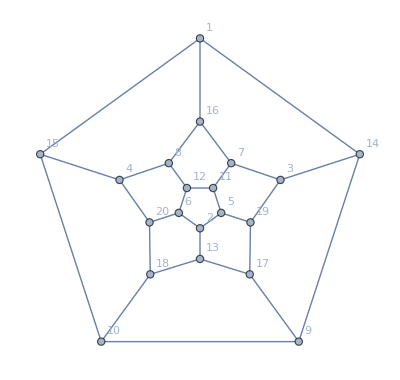

```mathematica
graphFromG[dodeca]
```

```mathematica
root={1.6838616297871791,3.5522063477126107,0.5291610914079277,3.5522063477126107,1.6838616297871791,3.5522063477126107,-0.18448308813825243,1.6838616297871791,3.5522063477126107,4.706906886091862,0.5291610914079277,1.6838616297871791,4.706906886091862,1.6838616297871791,3.5522063477126107,0.5291610914079277,3.5522063477126107,5.420551065638042,1.6838616297871791,4.706906886091862};
```

```mathematica
(*fractalDimensionFromG[G,10000,100,root]*)
```

```mathematica
W={{0, 0, 0, -1}, {2, 0, 0, 1}, {0, 3, 0, 1}, {2, 3, √3, 2}};
```

```mathematica
P={{0, -1/2, 0, 0}, {-1/2, 0, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}};
```

```mathematica
G={{1, -1, -1, -2}, {-1, 1, -2, -1}, {-1, -2, 1, -1}, {-2, -1, -1, 1}};
```

```mathematica
W.P.Transpose[W]//MatrixForm
```

(1 | -1 | -1 | -2
-1 | 1 | -2 | -1
-1 | -2 | 1 | -1
-2 | -1 | -1 | 1)

```mathematica
v=Table[Subscript[b, i],{i,4}]
```

{b_1,b_2,b_3,b_4}

```mathematica
eq=Simplify[v.Inverse[G].v]==0
```

1/3 (b_1^2+b_2^2-2 b_1 (b_2+b_3)+(b_3-b_4)^2-2 b_2 b_4)==0

```mathematica
Total[Solve[eq,Subscript[b, 4]]/.{Subscript[b, 4]->x_}->x]
```

2 b_2+2 b_3

```mathematica
sigmas={
{{-1, 2, 2, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}},{{1, 0, 0, 0}, {2, -1, 0, 2}, {0, 0, 1, 0}, {0, 0, 0, 1}},{{1, 0, 0, 0}, {0, 1, 0, 0}, {2, 0, -1, 2}, {0, 0, 0, 1}},{{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 2, 2, -1}}
};
```

```mathematica
faces={{2,3,4},{1,3,4},{1,2,4},{1,2,3}};
```

```mathematica
root={-2,4,5,9};
```

```mathematica
Total[sigmas⟦1⟧.v]
```

-b_1+3 b_2+3 b_3+b_4

```mathematica
eq/.{Subscript[b, 1]->-2,Subscript[b, 2]->4,Subscript[b, 3]->5}//Simplify
```

b_4==9

```mathematica
(*search[sigmas,N[root],-1,20]*)
```

```mathematica
sigmas={
{{-1, 2, 2, 2}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}},{{1, 0, 0, 0}, {2, -1, 2, 2}, {0, 0, 1, 0}, {0, 0, 0, 1}},{{1, 0, 0, 0}, {0, 1, 0, 0}, {2, 2, -1, 2}, {0, 0, 0, 1}},{{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {2, 2, 2, -1}}
};
faces={{2,3,4},{1,3,4},{1,2,4},{1,2,3}};
root={-6,11,14,23};
Timing[search[sigmas,N[root],{},2000,faces]+Length[root]]
```

{0.035684,794}

```mathematica
G={{1, -1, -1, -1}, {-1, 1, -1, -1}, {-1, -1, 1, -1}, {-1, -1, -1, 1}}
```

{{1,-1,-1,-1},{-1,1,-1,-1},{-1,-1,1,-1},{-1,-1,-1,1}}

```mathematica
(*fractalDimensionFromG[G,1000,100,root]*)
```

```mathematica
sigmas⟦1⟧.root
```

{102,11,14,23}

```mathematica
sigmas⟦2⟧.sigmas⟦3⟧.sigmas⟦2⟧.root//Total
```

366

```mathematica
Total[root]
```

42

```mathematica
Total[sigmas⟦4⟧.sigmas⟦3⟧.sigmas⟦4⟧.root]
```

78

```mathematica
(*search[generators_,current_,lastgen_,upperBound_]:=
Total[Table[If[(generators⟦i⟧.current)⟦i⟧≥upperBound||Total[generators⟦i⟧.current]≤Total[current],0,1+search[generators,generators⟦i⟧.current,i,upperBound]],{i,4}]]*)
```

```mathematica
sigmas⟦3⟧.root
```

{-6,11,42,23}

```mathematica
(*search[sigmas,N[root],{},10,faces]*)
```

```mathematica
(*max=100;
delta=10;
xs=Range[1,max,delta];
ys=search[sigmas,N[root],-1,#]+Length[root]&/@xs;
data={xs⟦#⟧,ys⟦#⟧}&/@Range[Length[ys]];
nlm=NonlinearModelFit[data,a x^b,{a,b},x];
params=nlm["BestFitParameters"];
b/.params*)
```

```mathematica
nlm["RSquared"]
```

nlm[RSquared]

```mathematica
G=pyramidG[4]//Simplify
```

{{1,-1,-1,-1,-1},{-1,1,-1,-3,-1},{-1,-1,1,-1,-3},{-1,-3,-1,1,-1},{-1,-1,-3,-1,1}}

```mathematica
sigmas=findGeneratorsFromG[G]
```

{{{1.,0.,0.,0.,0.},{0.,1.,0.,0.,0.},{4.,3.,0.,-1.,3.},{4.,2.,0.,-1.,4.},{0.,0.,0.,0.,1.}},{{1.,0.,0.,0.,0.},{0.,1.,0.,0.,0.},{0.,0.,1.,0.,0.},{4.,2.,4.,-1.,0.},{4.,3.,3.,-1.,0.}},{{1.,0.,0.,0.,0.},{4.,0.,3.,3.,-1.},{0.,0.,1.,0.,0.},{0.,0.,0.,1.,0.},{4.,0.,2.,4.,-1.}},{{1.,0.,0.,0.,0.},{4.,-1.,0.,2.,4.},{4.,-1.,0.,3.,3.},{0.,0.,0.,1.,0.},{0.,0.,0.,0.,1.}},{{-1.,1.,0.,1.,0.},{0.,1.,0.,0.,0.},{0.,1.,0.,1.,-1.},{0.,0.,0.,1.,0.},{0.,0.,0.,0.,1.}}}

```mathematica
FindFace[graphFromG[G]]-1
```

{{0,1,4},{0,2,1},{0,3,2},{0,4,3},{1,2,3,4}}

```mathematica
root={-0.5131807550506294,1.2389279387920946,1.2389279387920946,1.2389279387920946,1.2389279387920946}
```

{-0.513181,1.23893,1.23893,1.23893,1.23893}

```mathematica
sigmas⟦1⟧.root
```

{-0.513181,1.23893,4.14192,4.14192,1.23893}

```mathematica
octahedron={{1, -1, -1, -1, -1, -3}, {-1, 1, -1, -3, -1, -1}, {-1, -1, 1, -1, -3, -1}, {-1, -3, -1, 1, -1, -1}, {-1, -1, -3, -1, 1, -1}, {-3, -1, -1, -1, -1, 1}}
```

{{1,-1,-1,-1,-1,-3},{-1,1,-1,-3,-1,-1},{-1,-1,1,-1,-3,-1},{-1,-3,-1,1,-1,-1},{-1,-1,-3,-1,1,-1},{-3,-1,-1,-1,-1,1}}

```mathematica
sigmas=findGeneratorsFromG[octahedron]//RootApproximant
```

{{{1,0,0,0,0,0},{0,1,0,0,0,0},{4,4,-1,0,2,0},{4,3,-1,0,3,0},{0,0,0,0,1,0},{3,4,-1,0,3,0}},{{1,0,0,0,0,0},{0,1,0,0,0,0},{0,0,1,0,0,0},{3,3,4,0,0,-1},{3,4,3,0,0,-1},{2,4,4,0,0,-1}},{{1,0,0,0,0,0},{4,-1,4,2,0,0},{0,0,1,0,0,0},{0,0,0,1,0,0},{4,-1,3,3,0,0},{3,-1,4,3,0,0}},{{1,0,0,0,0,0},{4,-1,0,2,4,0},{4,-1,0,3,3,0},{0,0,0,1,0,0},{0,0,0,0,1,0},{3,-1,0,3,4,0}},{{-1,4,4,0,0,2},{0,1,0,0,0,0},{0,0,1,0,0,0},{-1,3,4,0,0,3},{-1,4,3,0,0,3},{0,0,0,0,0,1}},{{0,3,0,-1,4,3},{0,1,0,0,0,0},{0,3,0,-1,3,4},{0,2,0,-1,4,4},{0,0,0,0,1,0},{0,0,0,0,0,1}},{{-1,0,4,4,0,2},{-1,0,4,3,0,3},{0,0,1,0,0,0},{0,0,0,1,0,0},{-1,0,3,4,0,3},{0,0,0,0,0,1}},{{-1,0,0,4,4,2},{-1,0,0,3,4,3},{-1,0,0,4,3,3},{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}}}

```mathematica
root={-1,2,2,4,4,7}
```

{-1,2,2,4,4,7}

```mathematica
sigmas⟦8⟧.root
```

{47,50,50,4,4,7}

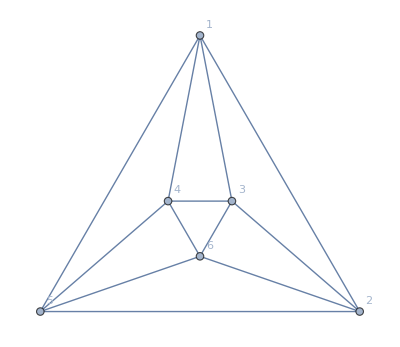

```mathematica
graphFromG[octahedron]
```

```mathematica
faces=FindFace[graphFromG[octahedron]]
```

{{1,2,5},{1,3,2},{1,4,3},{1,5,4},{2,3,6},{2,6,5},{3,4,6},{4,5,6}}

```mathematica
faces-1
```

{{0,1,4},{0,2,1},{0,3,2},{0,4,3},{1,2,5},{1,5,4},{2,3,5},{3,4,5}}

```mathematica
search[sigmas,root,{},20000,faces]
```

279753

```mathematica
penta=pyramidG[5]//Simplify
```

{{1,-1,-1,-1,-1,-1},{-1,1,-1,-2-√5,-2-√5,-1},{-1,-1,1,-1,-2-√5,-2-√5},{-1,-2-√5,-1,1,-1,-2-√5},{-1,-2-√5,-2-√5,-1,1,-1},{-1,-1,-2-√5,-2-√5,-1,1}}

```mathematica
faces=FindFace[graphFromG[penta]]
```

{{1,2,6},{1,3,2},{1,4,3},{1,5,4},{1,6,5},{2,3,4,5,6}}

```mathematica
sigmas=findGeneratorsFromG[penta]
```

{{{1.,0.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.},{5.23607,5.23607,-1.,0.,0.,2.},{8.47214,6.8541,-1.61803,0.,0.,4.23607},{5.23607,3.61803,-1.,0.,0.,3.61803},{0.,0.,0.,0.,0.,1.}},{{1.,0.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.},{0.,0.,1.,0.,0.,0.},{5.23607,2.,5.23607,-1.,0.,0.},{8.47214,4.23607,6.8541,-1.61803,0.,0.},{5.23607,3.61803,3.61803,-1.,0.,0.}},{{1.,0.,0.,0.,0.,0.},{5.23607,0.,4.23607,2.61803,0.,-0.618034},{0.,0.,1.,0.,0.,0.},{0.,0.,0.,1.,0.,0.},{5.23607,0.,2.61803,4.23607,0.,-0.618034},{8.47214,0.,5.23607,5.23607,0.,-1.}},{{1.,0.,0.,0.,0.,0.},{8.47214,-1.,0.,5.23607,5.23607,0.},{5.23607,-0.618034,0.,4.23607,2.61803,0.},{0.,0.,0.,1.,0.,0.},{0.,0.,0.,0.,1.,0.},{5.23607,-0.618034,0.,2.61803,4.23607,0.}},{{1.,0.,0.,0.,0.,0.},{5.23607,0.,-0.618034,0.,2.61803,4.23607},{8.47214,0.,-1.,0.,5.23607,5.23607},{5.23607,0.,-0.618034,0.,4.23607,2.61803},{0.,0.,0.,0.,1.,0.},{0.,0.,0.,0.,0.,1.}},{{-1.,0.291796,0.291796,0.,0.472136,0.},{0.,1.,0.,0.,0.,0.},{0.,0.,1.,0.,0.,0.},{0.,-0.618034,1.,0.,0.618034,0.},{0.,0.,0.,0.,1.,0.},{0.,1.,-0.618034,0.,0.618034,0.}}}

```mathematica
root={-0.5511585907448705,1.4888455922394608,1.4888455922394608,1.4888455922394608,1.4888455922394608,1.4888455922394608};
```

```mathematica
Total[root]
```

6.89307

```mathematica
faces
```

{{1,2,6},{1,3,2},{1,4,3},{1,5,4},{1,6,5},{2,3,4,5,6}}

```mathematica
root
```

{-0.551159,1.48885,1.48885,1.48885,1.48885,1.48885}

```mathematica
sigmas⟦3⟧.sigmas⟦2⟧.sigmas⟦1⟧.root//Total
```

352.792

```mathematica
(*pyramidFractalDimension[5,1000,100]*)
```

```mathematica
cube={{1, -1, -3, -1, -1, -3, -5, -3}, {-1, 1, -1, -3, -3, -1, -3, -5}, {-3, -1, 1, -1, -5, -3, -1, -3}, {-1, -3, -1, 1, -3, -5, -3, -1}, {-1, -3, -5, -3, 1, -1, -3, -1}, {-3, -1, -3, -5, -1, 1, -1, -3}, {-5, -3, -1, -3, -3, -1, 1, -1}, {-3, -5, -3, -1, -1, -3, -1, 1}}
```

{{1,-1,-3,-1,-1,-3,-5,-3},{-1,1,-1,-3,-3,-1,-3,-5},{-3,-1,1,-1,-5,-3,-1,-3},{-1,-3,-1,1,-3,-5,-3,-1},{-1,-3,-5,-3,1,-1,-3,-1},{-3,-1,-3,-5,-1,1,-1,-3},{-5,-3,-1,-3,-3,-1,1,-1},{-3,-5,-3,-1,-1,-3,-1,1}}

```mathematica
(faces=FindFace[graphFromG[cube]])-1
```

{{0,1,5,4},{0,3,2,1},{0,4,7,3},{1,2,6,5},{2,3,7,6},{4,5,6,7}}

```mathematica
sigmas=findGeneratorsFromG[cube]
```

{{{1.,0.,0.,0.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.,0.,0.},{1.,3.,0.,-1.,2.,0.,0.,0.},{2.,2.,0.,-1.,2.,0.,0.,0.},{0.,0.,0.,0.,1.,0.,0.,0.},{-1.,1.,0.,0.,1.,0.,0.,0.},{0.,3.,0.,-1.,3.,0.,0.,0.},{1.,2.,0.,-1.,3.,0.,0.,0.}},{{1.,0.,0.,0.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.,0.,0.},{0.,0.,1.,0.,0.,0.,0.,0.},{1.,-1.,1.,0.,0.,0.,0.,0.},{3.,1.,2.,0.,0.,-1.,0.,0.},{2.,2.,2.,0.,0.,-1.,0.,0.},{2.,1.,3.,0.,0.,-1.,0.,0.},{3.,0.,3.,0.,0.,-1.,0.,0.}},{{0.,0.,0.,1.,1.,0.,0.,-1.},{0.,0.,0.,3.,4.,-1.,0.,-1.},{0.,0.,0.,3.,3.,-1.,0.,0.},{0.,0.,0.,1.,0.,0.,0.,0.},{0.,0.,0.,0.,1.,0.,0.,0.},{0.,0.,0.,2.,4.,-1.,0.,0.},{0.,0.,0.,2.,3.,-1.,0.,1.},{0.,0.,0.,0.,0.,0.,0.,1.}},{{0.,1.,3.,-1.,0.,2.,0.,0.},{0.,1.,0.,0.,0.,0.,0.,0.},{0.,0.,1.,0.,0.,0.,0.,0.},{0.,0.,4.,-1.,0.,2.,0.,0.},{0.,0.,3.,-1.,0.,3.,0.,0.},{0.,0.,0.,0.,0.,1.,0.,0.},{0.,-1.,1.,0.,0.,1.,0.,0.},{0.,-1.,4.,-1.,0.,3.,0.,0.}},{{-1.,0.,0.,4.,0.,0.,2.,0.},{-1.,0.,0.,4.,0.,0.,3.,-1.},{0.,0.,0.,1.,0.,0.,1.,-1.},{0.,0.,0.,1.,0.,0.,0.,0.},{-1.,0.,0.,3.,0.,0.,2.,1.},{-1.,0.,0.,3.,0.,0.,3.,0.},{0.,0.,0.,0.,0.,0.,1.,0.},{0.,0.,0.,0.,0.,0.,0.,1.}},{{-1.,0.,0.,0.,2.,2.,0.,2.},{-1.,0.,0.,0.,1.,3.,0.,2.},{-1.,0.,0.,0.,0.,3.,0.,3.},{-1.,0.,0.,0.,1.,2.,0.,3.},{0.,0.,0.,0.,1.,0.,0.,0.},{0.,0.,0.,0.,0.,1.,0.,0.},{0.,0.,0.,0.,-1.,1.,0.,1.},{0.,0.,0.,0.,0.,0.,0.,1.}}}

```mathematica
search[sigmas,{-1,4,7,2,7,12,15,10},{},100,faces]+8
```

456

```mathematica
hex=pyramidG[6]
```

{{1,-1,-1,-1,-1,-1,-1},{-1,1,-1,-5,-7,-5,-1},{-1,-1,1,-1,-5,-7,-5},{-1,-5,-1,1,-1,-5,-7},{-1,-7,-5,-1,1,-1,-5},{-1,-5,-7,-5,-1,1,-1},{-1,-1,-5,-7,-5,-1,1}}

```mathematica
sigmas=findGeneratorsFromG[hex]
```

{{{1.,0.,0.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.,0.},{6.,4.,0.,0.,0.,-1.,4.},{12.,6.,0.,0.,0.,-2.,9.},{12.,5.,0.,0.,0.,-2.,10.},{6.,2.,0.,0.,0.,-1.,6.},{0.,0.,0.,0.,0.,0.,1.}},{{1.,0.,0.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.,0.},{0.,0.,1.,0.,0.,0.,0.},{6.,2.,6.,-1.,0.,0.,0.},{12.,5.,10.,-2.,0.,0.,0.},{12.,6.,9.,-2.,0.,0.,0.},{6.,4.,4.,-1.,0.,0.,0.}},{{1.,0.,0.,0.,0.,0.,0.},{6.,0.,4.,4.,-1.,0.,0.},{0.,0.,1.,0.,0.,0.,0.},{0.,0.,0.,1.,0.,0.,0.},{6.,0.,2.,6.,-1.,0.,0.},{12.,0.,5.,10.,-2.,0.,0.},{12.,0.,6.,9.,-2.,0.,0.}},{{1.,0.,0.,0.,0.,0.,0.},{12.,-1.,0.,8.,6.,0.,0.},{6.,-0.5,0.,5.,2.5,0.,0.},{0.,0.,0.,1.,0.,0.,0.},{0.,0.,0.,0.,1.,0.,0.},{6.,-0.5,0.,3.,4.5,0.,0.},{12.,-1.,0.,7.,7.,0.,0.}},{{1.,0.,0.,0.,0.,0.,0.},{12.,-1.,0.,0.,6.,8.,0.},{12.,-1.,0.,0.,7.,7.,0.},{6.,-0.5,0.,0.,4.5,3.,0.},{0.,0.,0.,0.,1.,0.,0.},{0.,0.,0.,0.,0.,1.,0.},{6.,-0.5,0.,0.,2.5,5.,0.}},{{1.,0.,0.,0.,0.,0.,0.},{6.,0.,0.,-0.5,0.,3.,4.5},{12.,0.,0.,-1.,0.,7.,7.},{12.,0.,0.,-1.,0.,8.,6.},{6.,0.,0.,-0.5,0.,5.,2.5},{0.,0.,0.,0.,0.,1.,0.},{0.,0.,0.,0.,0.,0.,1.}},{{-1.,0.,0.333333,0.,0.,0.333333,0.},{0.,0.,1.5,-1.,0.,0.5,0.},{0.,0.,1.,0.,0.,0.,0.},{0.,0.,0.,1.,0.,0.,0.},{0.,0.,-0.5,1.,0.,0.5,0.},{0.,0.,0.,0.,0.,1.,0.},{0.,0.,1.,-1.,0.,1.,0.}}}

```mathematica
FindFace[graphFromG[hex]]-1
```

{{0,1,6},{0,2,1},{0,3,2},{0,4,3},{0,5,4},{0,6,5},{1,2,3,4,5,6}}

```mathematica
pyramidTuple[n_]:=N[Table[If[i==n+1,-1,(Sec[π/n]+Tan[π/n])/Tan[π/n]],{i,n+1}]]
```

```mathematica
pyramidTuple[6]
```

{3.,3.,3.,3.,3.,3.,-1.}

```mathematica
(*search[sigmas,pyramidTuple[6],{},100,FindFace[graphFromG[hex]]]*)
```

```mathematica
squarepyramid=pyramidG[4]
```

{{1,-1,-1,-1,-1},{-1,1,-1,-3,-1},{-1,-1,1,-1,-3},{-1,-3,-1,1,-1},{-1,-1,-3,-1,1}}

```mathematica
generators=findGeneratorsFromG[squarepyramid]
```

{{{1.,0.,0.,0.,0.},{0.,1.,0.,0.,0.},{4.,4.,-1.,0.,2.},{4.,3.,-1.,0.,3.},{0.,0.,0.,0.,1.}},{{1.,0.,0.,0.,0.},{0.,1.,0.,0.,0.},{0.,0.,1.,0.,0.},{4.,2.,4.,-1.,0.},{4.,3.,3.,-1.,0.}},{{1.,0.,0.,0.,0.},{4.,0.,3.,3.,-1.},{0.,0.,1.,0.,0.},{0.,0.,0.,1.,0.},{4.,0.,2.,4.,-1.}},{{1.,0.,0.,0.,0.},{4.,0.,-1.,3.,3.},{4.,0.,-1.,4.,2.},{0.,0.,0.,1.,0.},{0.,0.,0.,0.,1.}},{{-1.,1.,0.,1.,0.},{0.,1.,0.,0.,0.},{0.,0.,1.,0.,0.},{0.,0.,0.,1.,0.},{0.,1.,-1.,1.,0.}}}

```mathematica
root=pyramidTuple[4]
```

{2.41421,2.41421,2.41421,2.41421,-1.}

```mathematica
faces=FindFace[graphFromG[squarepyramid]]
```

{{1,2,5},{1,3,2},{1,4,3},{1,5,4},{2,3,4,5}}